# Pion induced Drell-Yan

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Projects\pion-proton-DY

## Pion and Proton TMDs

### Packages and grids

```mathematica
Needs["ErrorBarPlots`"]
<<mstwpdf.m
?xf
?ReadPDFGrid
```

Mathematica package for MSTW PDFs
by Graeme Watt <Graeme.Watt(at)cern.ch>.
For information on usage, see ?ReadPDFGrid and ?xf.

The function xf[ih,x,q,f] returns x times the parton distribution of flavour f corresponding to eigenvector set ih, where ih=0 is the central set, at a given momentum fraction x and scale q in GeV.  Note that ih and f must be integers, and x and q must be numeric quantities.  The PDG convention is used for the flavour f (apart from the gluon has f=0, not 21), that is, f = -6, -5, -4, -3, -2, -1, 0, 1, 2, 3, 4, 5, 6 corresponds to tbar, bbar, cbar, sbar, ubar, dbar, g, d, u, s, c, b, t.  The valence quark distributions can also be obtained directly with f = 7, 8, 9, 10, 11, 12 corresponding to dv, uv, sv, cv, bv, tv.  The photon distribution is obtained with f = 13.

The function ReadPDFGrid[prefix,ih] reads the PDF grid corresponding to eigenvector set ih, where ih=0 is the central set, into memory from the location specified by prefix.

```mathematica
protonf1="Grids/mstw2008lo";ReadPDFGrid[protonf1,0];

protong1=ReadList["Grids/g1.dat",Real,RecordLists-> True];

SB=ReadList["Grids/SofferBound.dat", Real, RecordLists->True];

pionf1=ReadList["Grids/pion_mrss.dat",Real,RecordLists-> True];

Leopionh1p=ReadList["Grids/bmgamberg.dat",Real,RecordLists-> True];

Barbf1=ReadList["./Grids/Barbara/proton_xf1_u_d_ub_db.dat",Real,RecordLists-> True];
Barbf1Tp=ReadList["./Grids/Barbara/proton_xf1Tp_1stmoment_u_d_ub_db.dat",Real,RecordLists-> True];
Barbh1=ReadList["./Grids/Barbara/proton_xh1_u_d.dat",Real,RecordLists-> True];
Barbh1p=ReadList["./Grids/Barbara/proton_xh1p_1stmoment_u_d.dat",Real,RecordLists-> True];
Barbh1Tp=ReadList["./Grids/Barbara/proton_xh1Tp_2ndmoment_u_d.dat",Real,RecordLists-> True];
Barbh1Lp=ReadList["./Grids/Barbara/proton_xh1Lp_1stmoment_u_d.dat",Real,RecordLists-> True];

Barbpionf1= ReadList["./Grids/Barbara/pion_xf1_u_d.dat",Real,RecordLists-> True];
Barbpionh1p= ReadList["./Grids/Barbara/pion_xh1p_1stmoment_ub.dat",Real,RecordLists-> True];
```

PDF grid read from Grids/mstw2008lo.00.dat

### Parameters

```mathematica
(* a is the index for pion (beam) and b represents proton (target) *)
Ma=0.135;Mb=0.938;
stot=2*190*0.938;
Q2min=4.3^2;Q2max=8.5^2;
Subscript[e, 1]=2/3;Subscript[e, 2]=-1/3;Subscript[e, 3]=-1/3;

(* kwa and kwb are the Guassian widths and the arguments represent U=Unpolarized, T=Transversity, S=Sivers, BM=Boer-Mulders, P=Pretzelosity, WG=Worm-Gear (Subscript[h, 1L]^⊥) *) 
kwb["U"]=0.25;kwa["U"]=0.25; (* Widths from arxiv:1003.2190 *)
kwb["T"]=kwb["U"];kwb["WG"]=kwb["T"];kwa["BM"]=kwb["BM"];

(* Broadening for three different cases; [U,U],[P,U],[P,P] *)
(* A and B can be U,T,S,BM,P or WG labeling the TMDs*)
(* P[A] categorizes the TMDs to unpolarizes and polarized quark distributions *)
qw[A_,B_]:=δ[P[A],P[B]]
P[A_]:=If[A=="U","U","P"]
δ["U","U"]=δUU;δ["U","P"]=δPU;δ["P","U"]=δPU;δ["P","P"]=δPP;
δUU=1.5;δPP=1.2;δPU=1.3;

qw["U","U"]
qw["U","P"]
qw["BM","S"]
```

1.5

1.3

1.2

### Pion TMDs

#### Pion Collinear

```mathematica
(* MRSS *)
upip=Interpolation[Table[{{pionf1[[i,1]],pionf1[[i,2]]},pionf1[[i,3]]},{i,1,Length[pionf1]}]];
dpip=Interpolation[Table[{{pionf1[[i,1]],pionf1[[i,2]]},pionf1[[i,4]]},{i,1,Length[pionf1]}]];
spip=Interpolation[Table[{{pionf1[[i,1]],pionf1[[i,2]]},pionf1[[i,5]]},{i,1,Length[pionf1]}]];
ubpip=Interpolation[Table[{{pionf1[[i,1]],pionf1[[i,2]]},pionf1[[i,6]]},{i,1,Length[pionf1]}]];
dbpip=Interpolation[Table[{{pionf1[[i,1]],pionf1[[i,2]]},pionf1[[i,7]]},{i,1,Length[pionf1]}]];
sbpip=Interpolation[Table[{{pionf1[[i,1]],pionf1[[i,2]]},pionf1[[i,8]]},{i,1,Length[pionf1]}]];
upim=dpip;dpim=upip;spim=spip;ubpim=dbpip;dbpim=ubpip;sbpim=sbpip;
(*********************************************************************************)
(* Barbara's f1 for π^+ *)
Barbxf1uπ=Interpolation[Table[{Barbpionf1[[i,1]],Barbpionf1[[i,2]]},{i,1,Length[Barbpionf1]}]];
Barbxf1dπ=Interpolation[Table[{Barbpionf1[[i,1]],Barbpionf1[[i,3]]},{i,1,Length[Barbpionf1]}]];

(********************************************************************************)
```

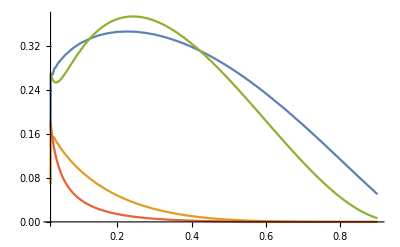

```mathematica
Plot[{x ubpim[x,28],x dbpim[x,28],Barbxf1uπ[x],Barbxf1dπ[x]},{x,0.02,0.9}]
```

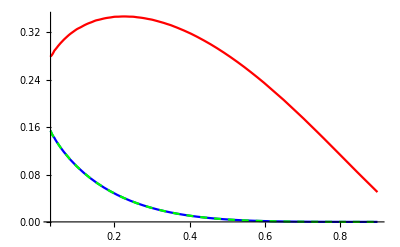

```mathematica
Plot[{ x upip[x,28],x dpip[x,28],x spip[x,28]},{x,0.03,0.9},PlotStyle->{Red,Blue,{Dashed,Green}}]
```

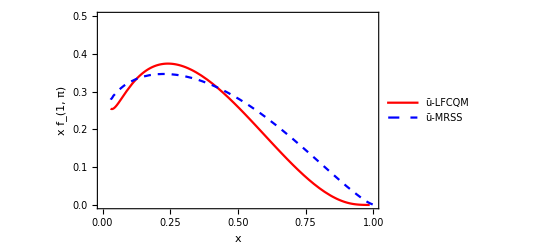

```mathematica
pionf1plot=Plot[{Barbxf1uπ[x],x upip[x,28]},{x,0.03,1.0},Frame-> True,FrameLabel-> {"x","x f_(1, π)"},BaseStyle-> {FontSize->12,FontFamily->"Times"},PlotRange-> {{0.001,1.0},{0,0.5}},PlotStyle->{Red,{Dashed,Blue}},PlotLegends->Placed[{Style["ū-LFCQM",12],Style["ū-MRSS",12]},{0.75,0.75}]]
```

```mathematica
Export["./Writeup/Figsupdate/xf1pion.pdf",pionf1plot,Background->None];
```

#### Pion Boer - Mulders

```mathematica
(*** BM^π from di-quark model. (-1) factor is due to sign flip of BM in DY ***)
Leoxh1perpπ=Interpolation[Table[{Leopionh1p[[i,1]],Leopionh1p[[i,2]]},{i,1,Length[Leopionh1p]}],InterpolationOrder->1];
Leoh1p1π[x_,Q2_]:=(-1)Leoxh1perpπ[x]/(x Ma^2);
Leoh1pπ[x_,Q2_]:=(-1)2 Leoxh1perpπ[x]/(x kwa["BM"]);

(* BM^π from LFCM Given for π^+. Note that h_(1 π^+)^(⊥u) = h_(1 π^-)^(⊥d̄) = h_(1 π^-)^(⊥ū) = h_(1 π^-)^(⊥d) *)
Barbxh1perp1uπ=Interpolation[Table[{Barbpionh1p[[i,1]],Barbpionh1p[[i,2]]},{i,1,Length[Barbpionh1p]}]];
```

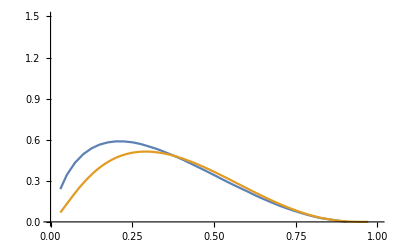

```mathematica
Plot[{  x Leoh1p1π[x,28], Barbxh1perp1uπ[x]},{x,0.03,1.0},PlotRange-> {0,1.5}]
```

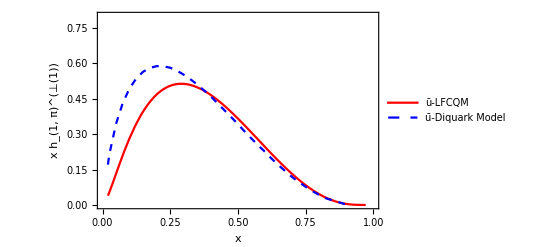

```mathematica
pionBMplot=Plot[{Barbxh1perp1uπ[x],x Leoh1p1π[x,28]},{x,0.02,1.0},Frame-> True,FrameLabel-> {"x","x h_(1, π)^(⊥(1))"},BaseStyle-> {FontSize->12,FontFamily->"Times"},PlotRange-> {{0.001,1.0},{0,0.8}},PlotStyle->{Red,{Dashed,Blue}},PlotLegends->Placed[{Style["ū-LFCQM",12],Style["ū-Diquark Model",12]},{0.75,0.75}]]
```

```mathematica
Export["./Writeup/Figsupdate/xh1p1pion.pdf",pionBMplot,Background->None];
```

### Proton TMDs

#### Unpolarized PDF

```mathematica
Clear[upv,dnv,usea,dsea,s,sb];
upv[x_,Q2_]:=xf[0,x,Sqrt[Q2],8]/x
dnv[x_,Q2_]:=xf[0,x,Sqrt[Q2],7]/x
usea[x_,Q2_]:=xf[0,x,Sqrt[Q2],-2]/x
dsea[x_,Q2_]:=xf[0,x,Sqrt[Q2],-1]/x
s[x_,Q2_]:=xf[0,x,Sqrt[Q2],3]/x
sb[x_,Q2_]:=xf[0,x,Sqrt[Q2],-3]/x
u[x_,Q2_]:=upv[x,Sqrt[Q2]]+usea[x,Sqrt[Q2]]
d[x_,Q2_]:=dnv[x,Sqrt[Q2]]+dsea[x,Sqrt[Q2]]
ub[x_,Q2_]:=usea[x,Sqrt[Q2]]
db[x_,Q2_]:=dsea[x,Sqrt[Q2]]


Barbxf1u=Interpolation[Table[{Barbf1[[i,1]],Barbf1[[i,2]]},{i,1,Length[Barbf1]}]];
Barbxf1d=Interpolation[Table[{Barbf1[[i,1]],Barbf1[[i,3]]},{i,1,Length[Barbf1]}]];
Barbxf1ub=Interpolation[Table[{Barbf1[[i,1]],Barbf1[[i,4]]},{i,1,Length[Barbf1]}]];
Barbxf1db=Interpolation[Table[{Barbf1[[i,1]],Barbf1[[i,5]]},{i,1,Length[Barbf1]}]];
```

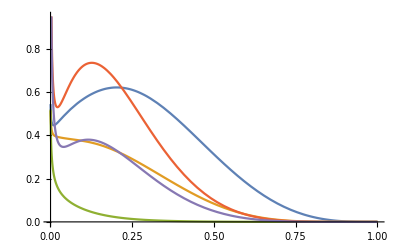

```mathematica
Plot[{x u[x,28],x d[x,28], x s[x,28],Barbxf1u[x],Barbxf1d[x]},{x,0.001,1.0}]
```

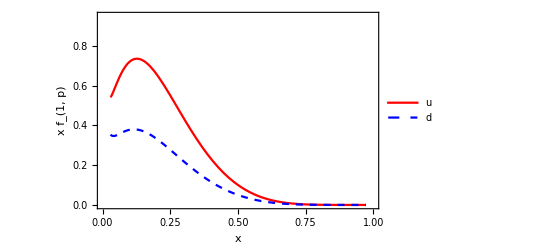

```mathematica
Plot[{Barbxf1u[x], Barbxf1d[x]},{x,0.03,1.0},Frame-> True,FrameLabel-> {"x","x f_(1, p)"},BaseStyle-> {FontSize->12,FontFamily->"Times"},PlotRange-> {{0.001,1.0},{0,0.95}},PlotStyle->{Red,{Dashed,Blue}},PlotLegends->Placed[{Style["u",12],Style["d",12]},{0.75,0.75}]]
```

```mathematica
Export["./Writeup/Figsupdate/xf1.pdf",Out[2030],Background->None];
```

#### Helicity PDF

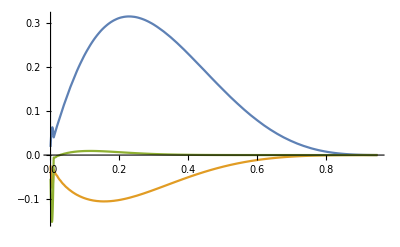

```mathematica
g1u=Interpolation[Table[{{protong1[[i,1]],protong1[[i,2]]},protong1[[i,3]]},{i,1,Length[protong1]}],InterpolationOrder->1];
g1d=Interpolation[Table[{{protong1[[i,1]],protong1[[i,2]]},protong1[[i,4]]},{i,1,Length[protong1]}],InterpolationOrder->1];
g1s=Interpolation[Table[{{protong1[[i,1]],protong1[[i,2]]},protong1[[i,5]]},{i,1,Length[protong1]}],InterpolationOrder->1];
g1ub=Interpolation[Table[{{protong1[[i,1]],protong1[[i,2]]},protong1[[i,6]]},{i,1,Length[protong1]}],InterpolationOrder->1];
g1db=Interpolation[Table[{{protong1[[i,1]],protong1[[i,2]]},protong1[[i,7]]},{i,1,Length[protong1]}],InterpolationOrder->1];
g1sb=Interpolation[Table[{{protong1[[i,1]],protong1[[i,2]]},protong1[[i,8]]},{i,1,Length[protong1]}],InterpolationOrder->1];
Plot[{x g1u[x,28],x g1d[x,28],x g1s[x,28]},{x,0.001,0.95}]
```

#### Soffer Bound

```mathematica
sbu=Interpolation[Table[{{SB[[i,1]],SB[[i,2]]},SB[[i,3]]},{i,1,Length[SB]}],InterpolationOrder-> {3,3}];
sbd=Interpolation[Table[{{SB[[i,1]],SB[[i,2]]},SB[[i,4]]},{i,1,Length[SB]}],InterpolationOrder-> {3,3}];sbs=Interpolation[Table[{{SB[[i,1]],SB[[i,2]]},SB[[i,5]]},{i,1,Length[SB]}],InterpolationOrder-> {3,3}];
sbub=Interpolation[Table[{{SB[[i,1]],SB[[i,2]]},SB[[i,6]]},{i,1,Length[SB]}],InterpolationOrder-> {3,3}];sbdb=Interpolation[Table[{{SB[[i,1]],SB[[i,2]]},SB[[i,7]]},{i,1,Length[SB]}],InterpolationOrder-> {3,3}];sbsb=Interpolation[Table[{{SB[[i,1]],SB[[i,2]]},SB[[i,8]]},{i,1,Length[SB]}],InterpolationOrder-> {3,3}];
```

#### Transversity

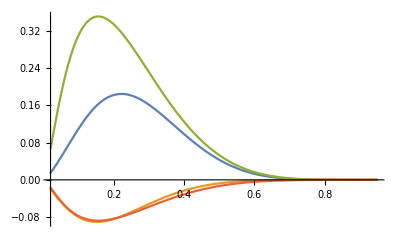

```mathematica
h1u[x_,Q2_]:=Subscript[N, Tu] x^α(1-x)^β(α+β)^(α+β)/(α^α β^β)sbu[x,Q2]
h1d[x_,Q2_]:=Subscript[N, Td] x^α(1-x)^β(α+β)^(α+β)/(α^α β^β)sbd[x,Q2]
Subscript[N, Tu]=0.46;Subscript[N, Td]=-1.0;α=1.11;β=3.64;

Barbxh1u=Interpolation[Table[{Barbh1[[i,1]],Barbh1[[i,2]]},{i,1,Length[Barbh1]}]];
Barbxh1d=Interpolation[Table[{Barbh1[[i,1]],Barbh1[[i,3]]},{i,1,Length[Barbh1]}]];

Plot[{x h1u[x,28],x h1d[x,28],Barbxh1u[x],Barbxh1d[x]},{x,0.02,0.95}]
h1u[.45,2.4];
```

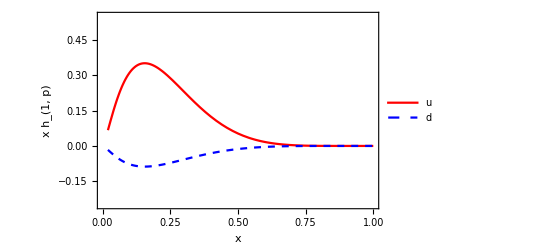

```mathematica
Plot[{Barbxh1u[x], Barbxh1d[x]},{x,0.02,1.0},Frame-> True,FrameLabel-> {"x","x h_(1, p)"},BaseStyle-> {FontSize->12,FontFamily->"Times"},PlotRange-> {{0.001,1.0},{-0.25,0.55}},PlotStyle->{Red,{Dashed,Blue}},PlotLegends->Placed[{Style["u",12],Style["d",12]},{0.75,0.75}]]
```

```mathematica
Export["./Writeup/Figsupdate/xh1.pdf",Out[1920],Background->None];
```

#### Sivers Function (DY)

```mathematica
MS=√0.19;
kwb["S"]=(kwb["U"] MS^2)/(kwb["U"]+MS^2);
atpS=-(-1)√(2ⅇ) (Mb kwb["S"])/(MS kwb["U"]);
(* The atpS is defined to map Alexie's parameterization to standard Gaussian form and (-1) is for DY sign flip *)
f1Tpu[x_,Q2_]:=atpS  Subscript[N, Su] x^Subscript[γ, u] (1-x)^Subscript[δ, u](Subscript[γ, u]+Subscript[δ, u])^(Subscript[γ, u]+Subscript[δ, u])/(Subscript[γ, u]^Subscript[γ, u] Subscript[δ, u]^Subscript[δ, u])u[x,Q2]
f1Tpd[x_,Q2_]:=atpS  Subscript[N, Sd] x^Subscript[γ, d] (1-x)^Subscript[δ, d](Subscript[γ, d]+Subscript[δ, d])^(Subscript[γ, d]+Subscript[δ, d])/(Subscript[γ, d]^Subscript[γ, d] Subscript[δ, d]^Subscript[δ, d])d[x,Q2]
Subscript[N, Su]=0.4;Subscript[N, Sd]=-0.97;
Subscript[γ, u]=0.35;Subscript[δ, u]=2.6;Subscript[γ, d]=0.44;Subscript[δ, d]=0.9;

f1Tp1u[x_,Q2_]:=kwb["S"]/(2 Mb^2) f1Tpu[x,Q2]
f1Tp1d[x_,Q2_]:=kwb["S"]/(2 Mb^2) f1Tpd[x,Q2]



Barbxf1Tperp1u=Interpolation[Table[{Barbf1Tp[[i,1]],Barbf1Tp[[i,2]]},{i,1,Length[Barbf1Tp]}]];
Barbxf1Tperp1d=Interpolation[Table[{Barbf1Tp[[i,1]],Barbf1Tp[[i,3]]},{i,1,Length[Barbf1Tp]}]];
Barbxf1Tperp1ub=Interpolation[Table[{Barbf1Tp[[i,1]],Barbf1Tp[[i,4]]},{i,1,Length[Barbf1Tp]}]];
Barbxf1Tperp1db=Interpolation[Table[{Barbf1Tp[[i,1]],Barbf1Tp[[i,5]]},{i,1,Length[Barbf1Tp]}]];
```

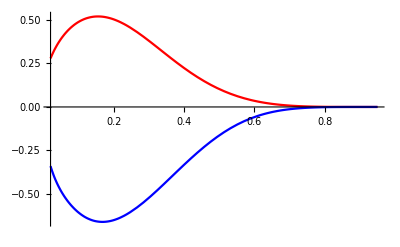

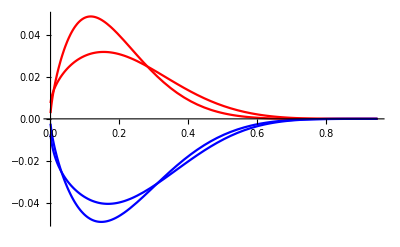

```mathematica
Plot[{x Sivu[x,28],x Sivd[x,28]},{x,0.02,0.95},PlotStyle->{Red,Blue}]
Plot[{x f1Tp1u[x,28],x f1Tp1d[x,28],Barbxf1Tperp1u[x],Barbxf1Tperp1d[x]},{x,0.001,0.95},PlotStyle->{Red,Blue}]
```

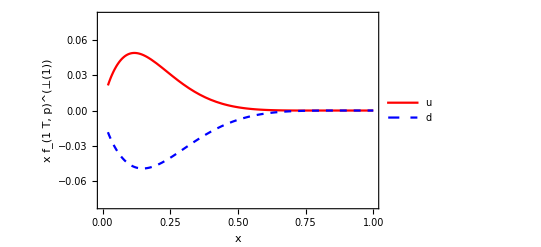

```mathematica
Plot[{Barbxf1Tperp1u[x], Barbxf1Tperp1d[x]},{x,0.02,1.0},Frame-> True,FrameLabel-> {"x","x f_(1  T, p)^(⊥(1))"},BaseStyle-> {FontSize->12,FontFamily->"Times"},PlotRange-> {{0.001,1.0},{-0.08,0.08}},PlotStyle->{Red,{Dashed,Blue}},PlotLegends->Placed[{Style["u",12],Style["d",12]},{0.75,0.75}]]
```

```mathematica
Export["./Writeup/Figsupdate/xf1Tp1.pdf",Out[1928],Background->None];
```

#### Pretzelosity

```mathematica
MTT=√0.18;
kwb["P"]=(kwb["U"] MTT^2)/(kwb["U"]+MTT^2);
atpP=ⅇ(Mb^2  kwb["P"])/(MTT^2  kwb["U"]) ;
(* atpP is defined to map Alexie's parameterization to standard Gaussian form *)
h1Tpu[x_,Q2_]:= atpP  Subscript[N, TTu] x^ϵ(1-x)^ζ(ϵ+ζ)^(ϵ+ζ)/(ϵ^ϵ ζ^ζ)(u[x,Q2]-g1u[x,Q2])
h1Tpd[x_,Q2_]:=atpP  Subscript[N, TTd] x^ϵ(1-x)^ζ(ϵ+ζ)^(ϵ+ζ)/(ϵ^ϵ ζ^ζ)(d[x,Q2]-g1d[x,Q2])
Subscript[N, TTu]=1.0;Subscript[N, TTd]=-1.0;ϵ=2.5;ζ=2.0;

h1Tp2u[x_,Q2_]:=kwb["P"]^2/(2 Mb^4) h1Tpu[x,Q2]
h1Tp2d[x_,Q2_]:=kwb["P"]^2/(2 Mb^4) h1Tpd[x,Q2]



Barbxh1Tperp2u=Interpolation[Table[{Barbh1Tp[[i,1]],Barbh1Tp[[i,2]]},{i,1,Length[Barbh1Tp]}]];
Barbxh1Tperp2d=Interpolation[Table[{Barbh1Tp[[i,1]],Barbh1Tp[[i,3]]},{i,1,Length[Barbh1Tp]}]];
```

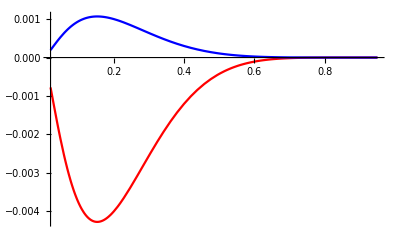

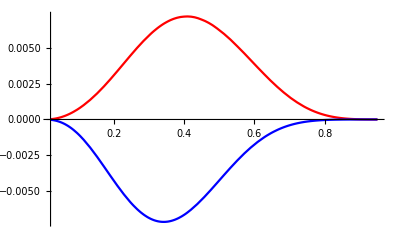

```mathematica
Plot[{Barbxh1Tperp2u[x],Barbxh1Tperp2d[x]},{x,0.02,0.95},PlotStyle->{Red,Blue}]

Plot[{x h1Tp2u[x,28],x h1Tp2d[x,28]},{x,0.02,0.95},PlotStyle->{Red,Blue}]
```

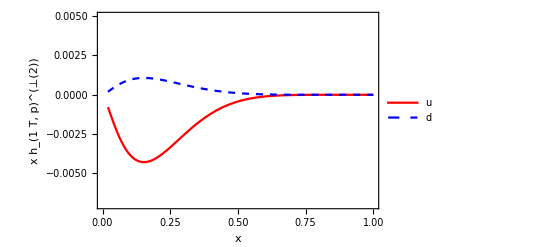

```mathematica
Plot[{Barbxh1Tperp2u[x], Barbxh1Tperp2d[x]},{x,0.02,1.0},Frame-> True,FrameLabel-> {"x","x h_(1  T, p)^(⊥(2))"},BaseStyle-> {FontSize->12,FontFamily->"Times"},PlotRange-> {{0.001,1.0},{-0.007,0.005}},PlotStyle->{Red,{Dashed,Blue}},PlotLegends->Placed[{Style["u",12],Style["d",12]},{0.75,0.25}]]
```

```mathematica
Export["./Writeup/Figsupdate/xh1Tp2.pdf",Out[1933],Background->None];
```

#### Boer-Moulders

```mathematica
MBM=√0.34;
kwb["BM"]=(kwb["U"] MBM^2)/(kwb["U"]+MBM^2);
atpBM=-(-1)kwb["BM"]/kwb["U"] Mb/MBM √(2 ⅇ);
(* The atpBM is defined to map Alexie's parameterization to standard Gaussian form and (-1) is for DY sign flip *)
h1pu[x_,Q2_]:=atpBM  Subscript[N, BMu] x^Subscript[σ, u](1-x)^Subscript[ρ, u](Subscript[σ, u]+Subscript[ρ, u])^(Subscript[σ, u]+Subscript[ρ, u])/(Subscript[σ, u]^Subscript[σ, u] Subscript[ρ, u]^Subscript[ρ, u]) u[x,Q2]
h1pd[x_,Q2_]:=atpBM  Subscript[N, BMd] x^Subscript[σ, d](1-x)^Subscript[ρ, d](Subscript[σ, d]+Subscript[ρ, d])^(Subscript[σ, d]+Subscript[ρ, d])/(Subscript[σ, d]^Subscript[σ, d] Subscript[ρ, d]^Subscript[ρ, d]) d[x,Q2]
Subscript[N, BMu]=2.1*0.35;Subscript[N, BMd]=-1.111*-0.9; 
Subscript[σ, u]=0.73; Subscript[ρ, u]=3.46;
Subscript[σ, d]=1.08; Subscript[ρ, d]=3.46;

h1p1u[x_,Q2_]:=kwb["BM"]/(2 Mb^2)h1pu[x,Q2]
h1p1d[x_,Q2_]:=kwb["BM"]/(2 Mb^2)h1pd[x,Q2]

Barbxh1perp1u=Interpolation[Table[{Barbh1p[[i,1]],Barbh1p[[i,2]]},{i,1,Length[Barbh1p]}]];
Barbxh1perp1d=Interpolation[Table[{Barbh1p[[i,1]],Barbh1p[[i,3]]},{i,1,Length[Barbh1p]}]];
```

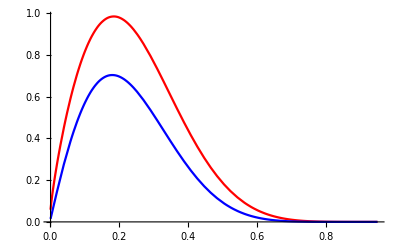

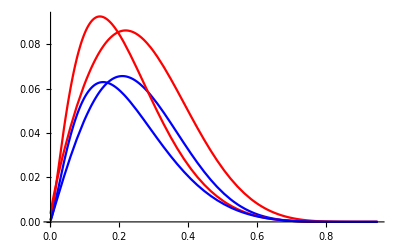

```mathematica
Plot[{x h1pu[x,28],x h1pd[x,28]},{x,0.002,0.95},PlotStyle->{Red,Blue}]
Plot[{x h1p1u[x,1.],x h1p1d[x,1.],Barbxh1perp1u[x],Barbxh1perp1d[x]},{x,0.002,0.95},PlotStyle->{Red,Blue}]
```

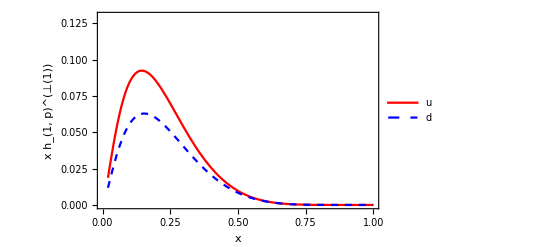

```mathematica
Plot[{Barbxh1perp1u[x], Barbxh1perp1d[x]},{x,0.02,1.0},Frame-> True,FrameLabel-> {"x","x h_(1, p)^(⊥(1))"},BaseStyle-> {FontSize->12,FontFamily->"Times"},PlotRange-> {{0.001,1.0},{0,0.13}},PlotStyle->{Red,{Dashed,Blue}},PlotLegends->Placed[{Style["u",12],Style["d",12]},{0.75,0.75}]]
```

```mathematica
Export["./Writeup/Figsupdate/xh1p1.pdf",Out[1937],Background->None];
```

#### h_(1L)^⊥ Worn-Gear

```mathematica
WW-Approximation

WWh1Lp1u[x_,Q2_]:=-x^2 NIntegrate[h1u[y,Q2]/y^2,{y,x,1}]
WWh1Lp1d[x_,Q2_]:= -x^2 NIntegrate[h1d[y,Q2]/y^2,{y,x,1}]

(* Export the calculated h1Lp1 for Q2=Qsquared *)
Dish1Lp1[Q2_]:= Table[{x,x WWh1Lp1u[x,Q2],x WWh1Lp1d[x,Q2]},{x,0.01,0.95,0.005}]
Qsquared=28;
Export["./Grids/xh1Lp1_u_d.dat",Dish1Lp1[Qsquared],"Table"];
```

WW-Approximation

```mathematica
h1Lp1=ReadList["./Grids/xh1Lp1_u_d.dat",Real,RecordLists-> True];
xh1Lp1u=Interpolation[Table[{h1Lp1[[i,1]],h1Lp1[[i,2]]},{i,1,Length[h1Lp1]}]];
xh1Lp1d=Interpolation[Table[{h1Lp1[[i,1]],h1Lp1[[i,3]]},{i,1,Length[h1Lp1]}]];

h1Lp1u[x_]:=xh1Lp1u[x]/x  
h1Lp1d[x_]:=xh1Lp1d[x]/x  


Barbxh1Lperp1u=Interpolation[Table[{Barbh1Lp[[i,1]],Barbh1Lp[[i,2]]},{i,1,Length[Barbh1Lp]}]];
Barbxh1Lperp1d=Interpolation[Table[{Barbh1Lp[[i,1]],Barbh1Lp[[i,3]]},{i,1,Length[Barbh1Lp]}]];
```

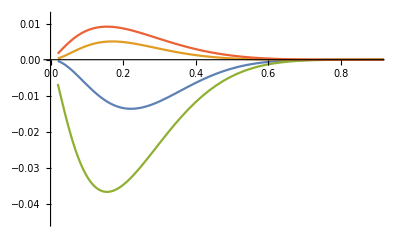

```mathematica
Plot[{x h1Lp1u[x],x h1Lp1d[x],Barbxh1Lperp1u[x],Barbxh1Lperp1d[x]},{x,0.02,0.95},PlotRange-> {{0,0.9},{-0.045,0.012}}]
```

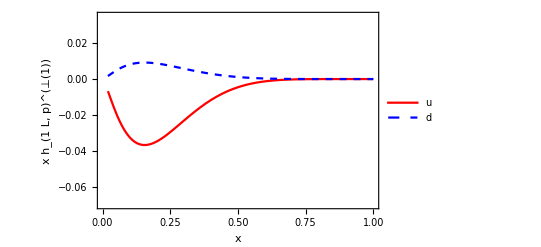

```mathematica
Plot[{Barbxh1Lperp1u[x], Barbxh1Lperp1d[x]},{x,0.02,1.0},Frame-> True,FrameLabel-> {"x","x h_(1  L, p)^(⊥(1))"},BaseStyle-> {FontSize->12,FontFamily->"Times",Black},PlotRange-> {{0.001,1.0},{-0.07,0.035}},PlotStyle->{Red,{Dashed,Blue}},PlotLegends->Placed[{Style["u",12],Style["d",12]},{0.75,0.25}]]
```

```mathematica
Export["./Writeup/Figsupdate/xh1Lp1.pdf",Out[1946],Background->None];
```

## Analytical Calculations of SFs

Defining Variables

```mathematica
Clear[x,qT,h]
Subscript[q, T]={Subscript[q, Tx],Subscript[q, Ty]};
hu:=Subscript[q, T]/Sqrt[Subscript[q, T].Subscript[q, T]]
Subscript[k, Ta]={Subscript[k, Tax],Subscript[k, Tay]};
Subscript[k, Tb]={Subscript[k, Tbx],Subscript[k, Tby]};
```

Convolution weight terms

```mathematica
w0=Subscript[k, Ta].Subscript[k, Tb]/(2 Subscript[M, a] Subscript[M, b]);
w1a=hu.Subscript[k, Ta]/Subscript[M, a];
w1b=hu.Subscript[k, Tb]/Subscript[M, b];
w2ab=(2 (hu.Subscript[k, Ta])(hu.Subscript[k, Tb])-Subscript[k, Ta].Subscript[k, Tb])/(Subscript[M, a] Subscript[M, b]);
w2aa=(2 (hu.Subscript[k, Ta])^2-Subscript[k, Ta].Subscript[k, Ta])/Subscript[M, a]^2;
w2bb=(2 (hu.Subscript[k, Tb])^2-Subscript[k, Tb].Subscript[k, Tb])/Subscript[M, b]^2;
w3ab=(2hu.Subscript[k, Ta] (2 (hu.Subscript[k, Ta])(hu.Subscript[k, Tb])-Subscript[k, Ta].Subscript[k, Tb])-(Subscript[k, Ta].Subscript[k, Ta])(hu.Subscript[k, Tb]))/(2 Subscript[M, a]^2 Subscript[M, b]);
w3ba=(2hu.Subscript[k, Tb](2 (hu.Subscript[k, Tb])(hu.Subscript[k, Ta])-Subscript[k, Tb].Subscript[k, Ta])-(Subscript[k, Tb].Subscript[k, Tb])(hu.Subscript[k, Ta]))/(2 Subscript[M, b]^2 Subscript[M, a]);
w4=(4 (hu.Subscript[k, Ta])(hu.Subscript[k, Tb])(2 (hu.Subscript[k, Ta])(hu.Subscript[k, Tb])-Subscript[k, Ta].Subscript[k, Tb])+(Subscript[k, Ta].Subscript[k, Ta])(Subscript[k, Tb].Subscript[k, Tb])-2(Subscript[k, Ta].Subscript[k, Ta])(hu.Subscript[k, Tb])^2-2(Subscript[k, Tb].Subscript[k, Tb])(hu.Subscript[k, Ta])^2)/(4 Subscript[M, a]^2 Subscript[M, b]^2);
w5=(2hu.Subscript[k, Tb](2(hu.Subscript[k, Ta])(hu.Subscript[k, Tb])-(Subscript[k, Ta].Subscript[k, Tb]))-(Subscript[k, Tb].Subscript[k, Tb])(hu.Subscript[k, Ta]))/(2 Subscript[M, b]^2 Subscript[M, a]);
```

TMDs Ansatz

```mathematica
TMDa[PDF_]:=Subscript[PDF, a] Exp[-Subscript[k, Ta].Subscript[k, Ta]/Subscript[kw, a]] /(Pi Subscript[kw, a])
OverBar[TMDa[PDF_]]:=Subscript[OverBar[PDF], a] Exp[-Subscript[k, Ta].Subscript[k, Ta]/Subscript[kw, a]] /(Pi Subscript[kw, a])
TMDb[PDF_]:=Subscript[PDF, b] Exp[-Subscript[k, Tb].Subscript[k, Tb]/Subscript[kw, b]] /(Pi Subscript[kw, b])
OverBar[TMDb[PDF_]]:=Subscript[OverBar[PDF], b] Exp[-Subscript[k, Tb].Subscript[k, Tb]/Subscript[kw, b]] /(Pi Subscript[kw, b])
```

Structure Functions

1/N_C∑_q e_q^2  is omitted, assume it is there and the TMDs carry parton index.

```mathematica
SF[w_,TMDa_,TMDb_]:=
Integrate[w(TMDa OverBar[TMDb]+OverBar[TMDa] TMDb)DiracDelta[Subscript[k, Tbx]-(Subscript[q, Tx]-Subscript[k, Tax])]DiracDelta[Subscript[k, Tby]-(Subscript[q, Ty]-Subscript[k, Tay])],{Subscript[k, Tax],-∞,+∞},{Subscript[k, Tay],-∞,+∞},{Subscript[k, Tbx],-∞,+∞},{Subscript[k, Tby],-∞,+∞},Assumptions->  Subscript[kw, a]>0 && Subscript[kw, b]>0 ]
```

```mathematica
test=SF[ w5,TMDa[Subscript[h, 1]],TMDb[Subscript[h, 1T]]]
```

(ⅇ^(-(q_Tx^2+q_Ty^2)/(kw_a+kw_b)) kw_a kw_b^2 (q_Tx^2+q_Ty^2)^(3/2) (OverBar[h_T]_b h_1_a+OverBar[h_1]_a h_T_b))/(2 π (kw_a+kw_b)^4 M_a M_b^2)

```mathematica
FUU1=SF[1,TMDa[Subscript[f, l]], TMDb[Subscript[f, l]]]
```

(ⅇ^(-(q_Tx^2+q_Ty^2)/(kw_a+kw_b)) (OverBar[f_l]_b f_l_a+OverBar[f_l]_a f_l_b))/(π (kw_a+kw_b))

```mathematica
FUUcos2ϕ=SF[w2ab,TMDa[Subscript[h, l]^ℶ],TMDb[Subscript[h, l]^ℶ]]
```

(ⅇ^(-(q_Tx^2+q_Ty^2)/(kw_a+kw_b)) kw_a kw_b (q_Tx^2+q_Ty^2) (OverBar[h_l^ℶ]_b (h_l^ℶ)_a+OverBar[h_l^ℶ]_a (h_l^ℶ)_b))/(π (kw_a+kw_b)^3 M_a M_b)

```mathematica
FLUsin2ϕ=SF[w2ab,TMDa[Subscript[h, lL]^ℶ],TMDb[Subscript[h, l]^ℶ]]
```

(ⅇ^(-(q_Tx^2+q_Ty^2)/(kw_a+kw_b)) kw_a kw_b (q_Tx^2+q_Ty^2) (OverBar[h_lL^ℶ]_a (h_l^ℶ)_b+OverBar[h_l^ℶ]_b (h_lL^ℶ)_a))/(π (kw_a+kw_b)^3 M_a M_b)

```mathematica
FULsin2ϕ=-SF[w2ab,TMDa[Subscript[h, l]^ℶ],TMDb[Subscript[h, lL]^ℶ]]
```

-(ⅇ^(-(q_Tx^2+q_Ty^2)/(kw_a+kw_b)) kw_a kw_b (q_Tx^2+q_Ty^2) (OverBar[h_lL^ℶ]_b (h_l^ℶ)_a+OverBar[h_l^ℶ]_a (h_lL^ℶ)_b))/(π (kw_a+kw_b)^3 M_a M_b)

```mathematica
FTU1=-SF[w1a,TMDa[Subscript[f, lT]^ℶ],TMDb[Subscript[f, l]]]
```

-(ⅇ^(-(q_Tx^2+q_Ty^2)/(kw_a+kw_b)) kw_a √(q_Tx^2+q_Ty^2) (OverBar[f_lT^ℶ]_a f_l_b+OverBar[f_l]_b (f_lT^ℶ)_a))/(π (kw_a+kw_b)^2 M_a)

```mathematica
FTUsin2ϕmϕa=SF[w1b,TMDa[Subscript[h, l]],TMDb[Subscript[h, l]^ℶ]]
```

(ⅇ^(-(q_Tx^2+q_Ty^2)/(kw_a+kw_b)) kw_b √(q_Tx^2+q_Ty^2) (OverBar[h_l^ℶ]_b h_l_a+OverBar[h_l]_a (h_l^ℶ)_b))/(π (kw_a+kw_b)^2 M_b)

```mathematica
FTUsin2ϕpϕa=SF[w3ab,TMDa[Subscript[h, lT]^ℶ],TMDb[Subscript[h, l]^ℶ]]
```

(ⅇ^(-(q_Tx^2+q_Ty^2)/(kw_a+kw_b)) kw_a^2 kw_b (q_Tx^2+q_Ty^2)^(3/2) (OverBar[h_lT^ℶ]_a (h_l^ℶ)_b+OverBar[h_l^ℶ]_b (h_lT^ℶ)_a))/(2 π (kw_a+kw_b)^4 M_a^2 M_b)

```mathematica
FUT1=SF[w1b,TMDa[Subscript[f, l]],TMDb[Subscript[f, lT]^ℶ]]
```

(ⅇ^(-(q_Tx^2+q_Ty^2)/(kw_a+kw_b)) kw_b √(q_Tx^2+q_Ty^2) (OverBar[f_lT^ℶ]_b f_l_a+OverBar[f_l]_a (f_lT^ℶ)_b))/(π (kw_a+kw_b)^2 M_b)

```mathematica
FUTsin2ϕmϕb=-SF[w1a,TMDa[Subscript[h, l]^ℶ],TMDb[Subscript[h, l]]]
```

-(ⅇ^(-(q_Tx^2+q_Ty^2)/(kw_a+kw_b)) kw_a √(q_Tx^2+q_Ty^2) (OverBar[h_l^ℶ]_a h_l_b+OverBar[h_l]_b (h_l^ℶ)_a))/(π (kw_a+kw_b)^2 M_a)

```mathematica
FUTsin2ϕpϕb=-SF[w3ba,TMDa[Subscript[h, l]^ℶ],TMDb[Subscript[h, lT]^ℶ]]
```

-(ⅇ^(-(q_Tx^2+q_Ty^2)/(kw_a+kw_b)) kw_a kw_b^2 (q_Tx^2+q_Ty^2)^(3/2) (OverBar[h_lT^ℶ]_b (h_l^ℶ)_a+OverBar[h_l^ℶ]_a (h_lT^ℶ)_b))/(2 π (kw_a+kw_b)^4 M_a M_b^2)

```mathematica
FLL1=-SF[1,TMDa[Subscript[g, lL]],TMDb[Subscript[g, lL]]]
```

-(ⅇ^(-(q_Tx^2+q_Ty^2)/(kw_a+kw_b)) (OverBar[g_lL]_b g_lL_a+OverBar[g_lL]_a g_lL_b))/(π (kw_a+kw_b))

```mathematica
FLLcos2ϕ=SF[w2ab,TMDa[Subscript[h, lL]^ℶ],TMDb[Subscript[h, lL]^ℶ]]
```

(ⅇ^(-(q_Tx^2+q_Ty^2)/(kw_a+kw_b)) kw_a kw_b (q_Tx^2+q_Ty^2) (OverBar[h_lL^ℶ]_b (h_lL^ℶ)_a+OverBar[h_lL^ℶ]_a (h_lL^ℶ)_b))/(π (kw_a+kw_b)^3 M_a M_b)

```mathematica
FLT1=-SF[w1b,TMDa[Subscript[g, lL]],TMDb[Subscript[g, lT]]]
```

-(ⅇ^(-(q_Tx^2+q_Ty^2)/(kw_a+kw_b)) kw_b √(q_Tx^2+q_Ty^2) (OverBar[g_lT]_b g_lL_a+OverBar[g_lL]_a g_lT_b))/(π (kw_a+kw_b)^2 M_b)

```mathematica
FLTcos2ϕmϕb=SF[w1a,TMDa[Subscript[h, lL]^ℶ],TMDb[Subscript[h, l]]]
```

(ⅇ^(-(q_Tx^2+q_Ty^2)/(kw_a+kw_b)) kw_a √(q_Tx^2+q_Ty^2) (OverBar[h_lL^ℶ]_a h_l_b+OverBar[h_l]_b (h_lL^ℶ)_a))/(π (kw_a+kw_b)^2 M_a)

```mathematica
FLTcos2ϕpϕb=SF[w3ba,TMDa[Subscript[h, lL]^ℶ],TMDb[Subscript[h, lT]^ℶ]]
```

(ⅇ^(-(q_Tx^2+q_Ty^2)/(kw_a+kw_b)) kw_a kw_b^2 (q_Tx^2+q_Ty^2)^(3/2) (OverBar[h_lT^ℶ]_b (h_lL^ℶ)_a+OverBar[h_lL^ℶ]_a (h_lT^ℶ)_b))/(2 π (kw_a+kw_b)^4 M_a M_b^2)

```mathematica
FTL1=-SF[w1a,TMDa[Subscript[g, lT]],TMDb[Subscript[g, lL]]]
```

-(ⅇ^(-(q_Tx^2+q_Ty^2)/(kw_a+kw_b)) kw_a √(q_Tx^2+q_Ty^2) (OverBar[g_lT]_a g_lL_b+OverBar[g_lL]_b g_lT_a))/(π (kw_a+kw_b)^2 M_a)

```mathematica
FTLcos2ϕmϕb=SF[w1b,TMDa[Subscript[h, l]],TMDb[Subscript[h, lL]^ℶ]]
```

(ⅇ^(-(q_Tx^2+q_Ty^2)/(kw_a+kw_b)) kw_b √(q_Tx^2+q_Ty^2) (OverBar[h_lL^ℶ]_b h_l_a+OverBar[h_l]_a (h_lL^ℶ)_b))/(π (kw_a+kw_b)^2 M_b)

```mathematica
FTLcos2ϕpϕb=SF[w3ab,TMDa[Subscript[h, lT]^ℶ],TMDb[Subscript[h, lL]^ℶ]]
```

(ⅇ^(-(q_Tx^2+q_Ty^2)/(kw_a+kw_b)) kw_a^2 kw_b (q_Tx^2+q_Ty^2)^(3/2) (OverBar[h_lT^ℶ]_a (h_lL^ℶ)_b+OverBar[h_lL^ℶ]_b (h_lT^ℶ)_a))/(2 π (kw_a+kw_b)^4 M_a^2 M_b)

```mathematica
FTT1=SF[w2ab,TMDa[Subscript[f, lT]^ℶ],TMDb[Subscript[f, lT]^ℶ]]-SF[w2ab,TMDa[Subscript[g, lT]],TMDb[Subscript[g, lT]]]
```

(ⅇ^(-(q_Tx^2+q_Ty^2)/(kw_a+kw_b)) kw_a kw_b (q_Tx^2+q_Ty^2) (OverBar[f_lT^ℶ]_b (f_lT^ℶ)_a+OverBar[f_lT^ℶ]_a (f_lT^ℶ)_b))/(π (kw_a+kw_b)^3 M_a M_b)-(ⅇ^(-(q_Tx^2+q_Ty^2)/(kw_a+kw_b)) kw_a kw_b (q_Tx^2+q_Ty^2) (OverBar[g_lT]_b g_lT_a+OverBar[g_lT]_a g_lT_b))/(π (kw_a+kw_b)^3 M_a M_b)

```mathematica
OverBar[FTT1]=-SF[w0,TMDa[Subscript[f, lT]^ℶ],TMDb[Subscript[f, lT]^ℶ]]-SF[w0,TMDa[Subscript[g, lT]],TMDb[Subscript[g, lT]]]
```

(ⅇ^(-(q_Tx^2+q_Ty^2)/(kw_a+kw_b)) kw_a √kw_b (√(kw_b^3 (kw_a+kw_b))+√(kw_b (kw_a+kw_b)) (kw_a-q_Tx^2-q_Ty^2)) (OverBar[f_lT^ℶ]_b (f_lT^ℶ)_a+OverBar[f_lT^ℶ]_a (f_lT^ℶ)_b))/(2 π (kw_a+kw_b)^(7/2) M_a M_b)+(ⅇ^(-(q_Tx^2+q_Ty^2)/(kw_a+kw_b)) kw_a √kw_b (√(kw_b^3 (kw_a+kw_b))+√(kw_b (kw_a+kw_b)) (kw_a-q_Tx^2-q_Ty^2)) (OverBar[g_lT]_b g_lT_a+OverBar[g_lT]_a g_lT_b))/(2 π (kw_a+kw_b)^(7/2) M_a M_b)

```mathematica
FTTcos2ϕmϕamϕb=SF[1,TMDa[Subscript[h, l]],TMDb[Subscript[h, l]]]
```

(ⅇ^(-(q_Tx^2+q_Ty^2)/(kw_a+kw_b)) (OverBar[h_l]_b h_l_a+OverBar[h_l]_a h_l_b))/(π (kw_a+kw_b))

```mathematica
FTTcos2ϕmϕapϕb=SF[w2bb,TMDa[Subscript[h, l]],TMDb[Subscript[h, lT]^ℶ]]
```

(ⅇ^(-(q_Tx^2+q_Ty^2)/(kw_a+kw_b)) kw_b^2 (q_Tx^2+q_Ty^2) (OverBar[h_lT^ℶ]_b h_l_a+OverBar[h_l]_a (h_lT^ℶ)_b))/(π (kw_a+kw_b)^3 M_b^2)

```mathematica
FTTcos2ϕpϕamϕb=SF[w2aa,TMDa[Subscript[h, lT]^ℶ],TMDb[Subscript[h, l]]]
```

(ⅇ^(-(q_Tx^2+q_Ty^2)/(kw_a+kw_b)) kw_a^2 (q_Tx^2+q_Ty^2) (OverBar[h_lT^ℶ]_a h_l_b+OverBar[h_l]_b (h_lT^ℶ)_a))/(π (kw_a+kw_b)^3 M_a^2)

```mathematica
FTTcos2ϕpϕapϕb=SF[w4,TMDa[Subscript[h, lT]^ℶ],TMDb[Subscript[h, lT]^ℶ]]
```

(ⅇ^(-(q_Tx^2+q_Ty^2)/(kw_a+kw_b)) kw_a^2 kw_b^2 (q_Tx^2+q_Ty^2)^2 (OverBar[h_lT^ℶ]_b (h_lT^ℶ)_a+OverBar[h_lT^ℶ]_a (h_lT^ℶ)_b))/(4 π (kw_a+kw_b)^5 M_a^2 M_b^2)

Helpful Integrals

```mathematica
qint1=2π ∫_0^(+∞) ⅇ^(-q^2/w)q^2 ⅆq
```

ConditionalExpression[1/2 π^(3/2) w^(3/2),Re[w]>0]

```mathematica
qint2=2π ∫_0^(+∞) ⅇ^(-q^2/w)q^3 ⅆq
```

ConditionalExpression[3/4 π^(3/2) w^(5/2),Re[w]>0]

```mathematica
qint3=2π ∫_0^(+∞) ⅇ^(-q^2/w)q^4 ⅆq
```

ConditionalExpression[π w^2,Re[w]>0]

## Kinematics

x-Cuts

```mathematica
inf=10000;
xa[xb_,Q2_]:=Q2/(stot xb)
xpixN=Manipulate[Plot[{1,inf (xb-.9999),xa[xb,Q2min],xa[xb,Q2max],xa[xb,Q2]},{xb,0,1.001},PlotRange-> {{0,1.001},{0,1.001}},Frame->True,AspectRatio->1],{Q2,Q2min,Q2max}]
```

```mathematica
ManToGif[man_,name_String,step_Integer]:=Export[name<>".gif",Import[Export[FileNameJoin[{NotebookDirectory[],"test.avi"}],man],"ImageList"][[1;;-1;;step]]];

ManToGif[xpixN,FileNameJoin[{NotebookDirectory[],"test"}],1];
```

Q^2-Sensitivity check of  f_(1π)  and  f_(1p)

```mathematica
Manipulate[Plot[{u[Q2min/(stot xa),Q2min],u[Q2max/(stot xa),Q2max], u[Q2/(stot xa),Q2]},{xa,Q2max/stot,1},FrameLabel-> {"f_(1  N)^(TraditionalForm`u)","xb"},PlotRange->{0,10}],{Q2,Q2min,Q2max}]
Manipulate[Plot[{upip[Q2min/(stot xb),Q2min],upip[(Q2max-1)/(stot xb),Q2max], upip[Q2/(stot xb),Q2]},{xb,Q2max/stot,1},FrameLabel-> {"f_(1  π)^(TraditionalForm`u)","xa"},PlotRange-> {0,6}],{Q2,Q2min,Q2max}]
```

Plot::plln: Limiting value Q2max/stot in {xb,Q2max/stot,1} is not a machine-sized real number.

## Spin Asymmetries of π^- p DY

### FUU1

#### Numerical Calculations

```mathematica
(*** TMDs from MSTW and MRSS ***)

FUU1[xa_,xb_,Q2_,qT_]:=(ⅇ^(-qT^2/qw["U","U"]))/(π qw["U","U"]) ∑_(q=1)^3 Subscript[e, q]^2  (Subscript[f1b, q][xb,Q2] OverBar[Subscript[f1a, q]][xa,Q2]+Subscript[f1a, q][xa,Q2] OverBar[Subscript[f1b, q]][xb,Q2])

FUU1qint[xa_,xb_,Q2_]:=∑_(q=1)^3 Subscript[e, q]^2 (Subscript[f1b, q][xb,Q2] OverBar[Subscript[f1a, q]][xa,Q2]+Subscript[f1a, q][xa,Q2] OverBar[Subscript[f1b, q]][xb,Q2])

(* FUU1 integrated over xa. Dis- perform the integral for 10 qT values to be interploated later *)
FUU1qTa[Q2_,qT_]:=NIntegrate[FUU1[xa,Q2/(xa stot),Q2,qT],{xa,Q2/stot,1}]
DisFUU1qTa[Q2_,step_]:=Table[{qT,FUU1qTa[Q2,qT]},{qT,.02,2.2,step}]


(* FUU1 integrated over xb. Dis- calculates for 10 qT values *)
FUU1qTb[Q2_,qT_]:=NIntegrate[FUU1[Q2/(xb stot),xb,Q2,qT],{xb,Q2/stot,1}]
DisFUU1qTb[Q2_,step_]:=Table[{qT,FUU1qTb[Q2,qT]},{qT,.02,2.2,step}]



Subscript[f1a, 1][x_,Q2_]:=upim[x,Q2]; Subscript[f1a, 2][x_,Q2_]:=dpim[x,Q2]; Subscript[f1a, 3][x_,Q2_]:=spim[x,Q2]
OverBar[Subscript[f1a, 1]][x_,Q2_]:=ubpim[x,Q2]; OverBar[Subscript[f1a, 2]][x_,Q2_]:=dbpim[x,Q2]; OverBar[Subscript[f1a, 3]][x_,Q2_]:=sbpim[x,Q2]
Subscript[f1b, 1][x_,Q2_]:=u[x,Q2];Subscript[f1b, 2][x_,Q2_]:=d[x,Q2];Subscript[f1b, 3][x_,Q2_]:=s[x,Q2]
OverBar[Subscript[f1b, 1]][x_,Q2_]:=ub[x,Q2]; OverBar[Subscript[f1b, 2]][x_,Q2_]:=db[x,Q2]; OverBar[Subscript[f1b, 3]][x_,Q2_]:=sb[x,Q2]
```

```mathematica
(*** TMDs from Barbara's model ***)
(* B in front of a TMD means it is from Barbara's model *)

BarbFUU1[xa_,xb_,Q2_,qT_]:=(ⅇ^(-qT^2/qw["U","U"]))/(π qw["U","U"])∑_(q=1)^2 Subscript[e, q]^2(Subscript[Bf1b, q][xb,Q2] OverBar[Subscript[Bf1a, q]][xa,Q2]+Subscript[Bf1a, q][xa,Q2] OverBar[Subscript[Bf1b, q]][xb,Q2])
BarbFUU1qint[xa_,xb_,Q2_]:=∑_(q=1)^2 Subscript[e, q]^2 (Subscript[Bf1b, q][xb,Q2] OverBar[Subscript[Bf1a, q]][xa,Q2]+Subscript[Bf1a, q][xa,Q2] OverBar[Subscript[Bf1b, q]][xb,Q2])

BarbFUU1qTa[Q2_,qT_]:=NIntegrate[BarbFUU1[xa,Q2/(xa stot),Q2,qT],{xa,Q2/stot,1}]
DisBarbFUU1qTa[Q2_,step_]:=Table[{qT,BarbFUU1qTa[Q2,qT]},{qT,.02,2.2,step}]


BarbFUU1qTb[Q2_,qT_]:=NIntegrate[BarbFUU1[Q2/(xb stot),xb,Q2,qT],{xb,Q2/stot,1}]
DisBarbFUU1qTb[Q2_,step_]:=Table[{qT,BarbFUU1qTb[Q2,qT]},{qT,.02,2.2,step}]



Subscript[Bf1a, 1][x_,Q2_]:=Barbxf1dπ[x]/x; Subscript[Bf1a, 2][x_,Q2_]:=Barbxf1uπ[x]/x; (* Subscript[Bf1a, 3][x_,Q2_]:=Barbf1sπ[x,Q2];*)
OverBar[Subscript[Bf1a, 1]][x_,Q2_]:=Barbxf1uπ[x]/x; OverBar[Subscript[Bf1a, 2]][x_,Q2_]:=Barbxf1dπ[x]/x; (* OverBar[Subscript[Bf1a, 3]][x_,Q2_]:=Barbsbpim[x,Q2];*)

Subscript[Bf1b, 1][x_,Q2_]:=Barbxf1u[x]/x; Subscript[Bf1b, 2][x_,Q2_]:=Barbxf1d[x]/x; (*Subscript[Bf1b, 3][x_,Q2_]:=Barbspim[x,Q2];*)
OverBar[Subscript[Bf1b, 1]][x_,Q2_]:=Barbxf1ub[x]/x; OverBar[Subscript[Bf1b, 2]][x_,Q2_]:=Barbxf1db[x]/x;(* OverBar[Subscript[Bf1b, 3]][x,Q2]:=Barbsbpim[x,Q2]; *)
```

#### Plots

```mathematica
shortFUU1qTa=Interpolation[DisFUU1qTa[28,.2]];
shortFUU1qTb=Interpolation[DisFUU1qTb[28,.2]];
shortBarbFUU1qTa=Interpolation[DisBarbFUU1qTa[28,.2]];
shortBarbFUU1qTb=Interpolation[DisBarbFUU1qTb[28,.2]];
```

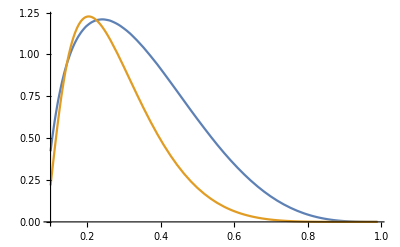

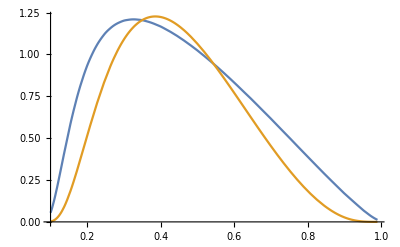

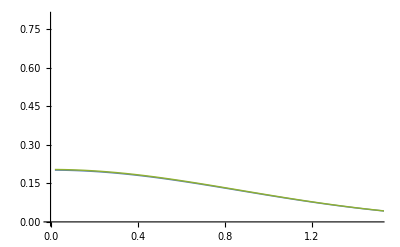

-Graphics-

```mathematica
Plot[{FUU1qint[28/(xb stot),xb,28],BarbFUU1qint[28/(xb stot),xb,28]},{xb,0.1,0.99}]

Plot[{FUU1qint[xa,28/(xa stot),28],BarbFUU1qint[xa,28/(xa stot),28]},{xa,0.1,0.99}]

Plot[{FUU1[.5,.17,28,qT],shortFUU1qTa[qT],BarbFUU1[.5,.17,28,qT],shortBarbFUU1qTa[qT]},{qT,0.02,2.0},PlotRange-> {{0,1.5},{0,.8}},PlotStyle->{Thick,Dashed,Thick,Dashed}]

Plot[{FUU1[.5,.17,28,qT],shortFUU1qTb[qT],BarbFUU1[.5,.17,28,qT],shortBarbFUU1qTb[qT]},{qT,0.02,2.0},PlotRange-> {{0,1.5},{0,.8}},PlotStyle->{Thick,Dashed,Thick,Dashed}]
```

### A_UT

#### Numerical Calculations

```mathematica
(*** Using MRSSand MSTW ***)

AUT1[xa_,xb_,Q2_,qT_]:=FUT1[xa,xb,Q2,qT]/FUU1[xa,xb,Q2,qT]

AUT1qTa[Q2_,qT_]:=FUT1qTa[Q2,qT]/FUU1qTa[Q2,qT]
DisAUT1qTa[Q2_,step_]:=Table[{qT,AUT1qTa[Q2,qT]},{qT,0.02,2.2,step}]

AUT1qTb[Q2_,qT_]:=FUT1qTb[Q2,qT]/FUU1qTb[Q2,qT]
DisAUT1qTb[Q2_,step_]:=Table[{qT,AUT1qTb[Q2,qT]},{qT,0.02,2.2,step}]

AUT1qint[xa_,xb_,Q2_]:=FUT1qint[xa,xb,Q2]/FUU1qint[xa,xb,Q2]


FUT1[xa_,xb_,Q2_,qT_]:=(2Mb)/(π qw["U","S"]^2)qT ⅇ^(-qT^2/qw["U","S"])    ∑_(q=1)^3 Subscript[e, q]^2(OverBar[Subscript[f1Tp1b, q]][xb,Q2] Subscript[f1a, q][xa,Q2]+OverBar[Subscript[f1a, q]][xa,Q2] Subscript[f1Tp1b, q][xb,Q2]) 

FUT1qint[xa_,xb_,Q2_]:=(√π Mb)/(√qw["U","S"])  ∑_(q=1)^3 Subscript[e, q]^2 (OverBar[Subscript[f1Tp1b, q]][xb,Q2] Subscript[f1a, q][xa,Q2]+OverBar[Subscript[f1a, q]][xa,Q2] Subscript[f1Tp1b, q][xb,Q2])


FUT1qTa[Q2_,qT_]:=NIntegrate[FUT1[xa,Q2/(xa stot),Q2,qT],{xa,Q2/stot,1}]
FUT1qTb[Q2_,qT_]:=NIntegrate[FUT1[Q2/(xb stot),xb,Q2,qT],{xb,Q2/stot,1}]

Subscript[f1Tp1b, 1][x_,Q2_]:= f1Tp1u[x,Q2];Subscript[f1Tp1b, 2][x_,Q2_]:= f1Tp1d[x,Q2];Subscript[f1Tp1b, 3][x_,Q2_]:=0.
OverBar[Subscript[f1Tp1b, 1]][x_,Q2_]:=0.; OverBar[Subscript[f1Tp1b, 2]][x_,Q2_]:=0.;OverBar[Subscript[f1Tp1b, 3]][x_,Q2_]:=0.
```

```mathematica
(*** Using Barbara's model ***)

BarbAUT1[xa_,xb_,Q2_,qT_]:=BarbFUT1[xa,xb,Q2,qT]/BarbFUU1[xa,xb,Q2,qT]

BarbAUT1qTa[Q2_,qT_]:=BarbFUT1qTa[Q2,qT]/BarbFUU1qTa[Q2,qT]
DisBarbAUT1qTa[Q2_,step_]:=Table[{qT,BarbAUT1qTa[Q2,qT]},{qT,0.02,2.2,step}]

BarbAUT1qTb[Q2_,qT_]:=BarbFUT1qTb[Q2,qT]/BarbFUU1qTb[Q2,qT]
DisBarbAUT1qTb[Q2_,step_]:=Table[{qT,BarbAUT1qTb[Q2,qT]},{qT,0.02,2.2,step}]

BarbAUT1qint[xa_,xb_,Q2_]:=BarbFUT1qint[xa,xb,Q2]/BarbFUU1qint[xa,xb,Q2]


BarbFUT1[xa_,xb_,Q2_,qT_]:=∑_(q=1)^2 Subscript[e, q]^2(2Mb)/(π qw["U","S"]^2) qT ⅇ^(-qT^2/qw["U","S"])  (OverBar[Subscript[Bf1Tp1b, q]][xb,Q2] Subscript[Bf1a, q][xa,Q2]+OverBar[Subscript[Bf1a, q]][xa,Q2] Subscript[Bf1Tp1b, q][xb,Q2])

BarbFUT1qint[xa_,xb_,Q2_]:=∑_(q=1)^2 Subscript[e, q]^2(√π Mb)/(√qw["U","S"])(OverBar[Subscript[Bf1Tp1b, q]][xb,Q2] Subscript[Bf1a, q][xa,Q2]+OverBar[Subscript[Bf1a, q]][xa,Q2] Subscript[Bf1Tp1b, q][xb,Q2])
BarbFUT1qTa[Q2_,qT_]:=NIntegrate[BarbFUT1[xa,Q2/(xa stot),Q2,qT],{xa,Q2/stot,1}]
BarbFUT1qTb[Q2_,qT_]:=NIntegrate[BarbFUT1[Q2/(xb stot),xb,Q2,qT],{xb,Q2/stot,1}]

(* Subscript[Bf1a, q] were evaluated in the "Unpolarized SF" subsection *)
Subscript[Bf1Tp1b, 1][x_,Q2_]:=Barbxf1Tperp1u[x]/x;Subscript[Bf1Tp1b, 2][x_,Q2_]:=Barbxf1Tperp1d[x]/x;
OverBar[Subscript[Bf1Tp1b, 1]][x_,Q2_]:=Barbxf1Tperp1ub[x]/x;OverBar[Subscript[Bf1Tp1b, 2]][x_,Q2_]:=Barbxf1Tperp1db[x]/x;
```

#### Theoretical Plots

x_π-dependent

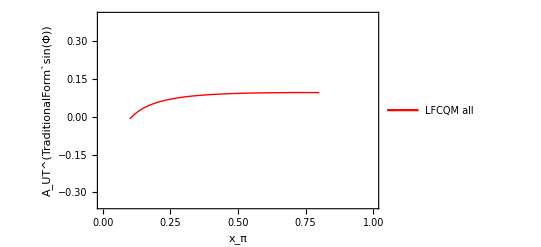

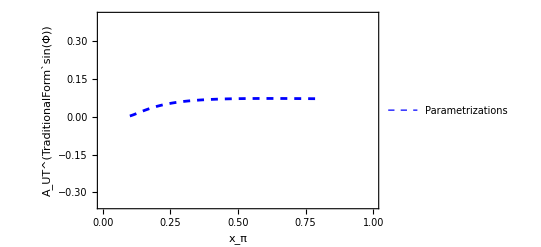

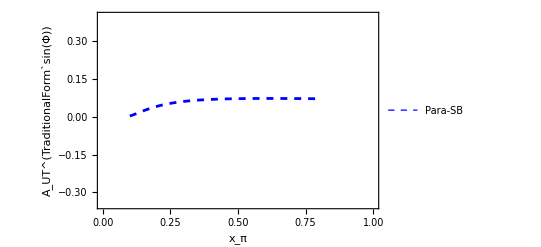

```mathematica
plotBarbAUT1xa=Plot[BarbAUT1qint[xa,28/(xa stot),28],{xa,0.1,0.8},PlotRange-> {{0,1.0},{-.35,0.4}},Frame->True,FrameLabel->{"x_π","A_UT^(TraditionalForm`sin(Φ))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Red,Thick}},PlotLegends->Placed[{Style["LFCQM all",9.5]},{0.75,0.25}]]

plotAUT1xa=Plot[AUT1qint[xa,28/(xa stot),28],{xa,0.1,0.8},PlotRange-> {{0,1.0},{-.35,0.4}},Frame->True,FrameLabel->{"x_π","A_UT^(TraditionalForm`sin(Φ))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Blue,Dashed,Thickness[0.005]}},PlotLegends->Placed[{Style["Parametrizations",9.5]},{0.75,0.15}]]

(* For legend adjustments: *)
plotAUT1xa2=Plot[AUT1qint[xa,28/(xa stot),28],{xa,0.1,0.8},PlotRange-> {{0,1.0},{-.35,0.4}},Frame->True,FrameLabel->{"x_π","A_UT^(TraditionalForm`sin(Φ))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Blue,Dashed,Thickness[0.005]}},PlotLegends->Placed[{Style["Para-SB",9.5]},{0.75,0.25}]]
```

x_p-dependent

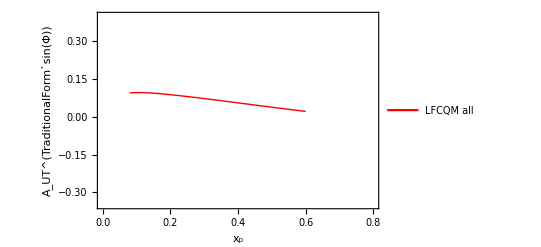

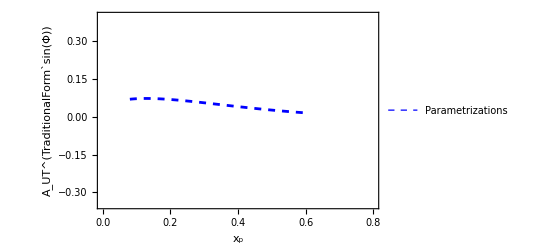

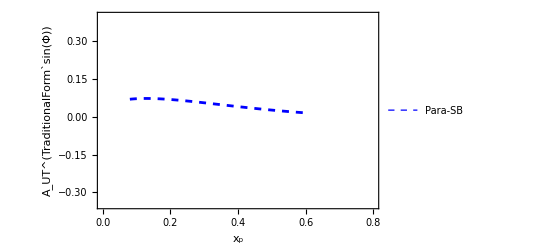

```mathematica
plotBarbAUT1xb=Plot[BarbAUT1qint[28/(xb stot),xb,28],{xb,0.0801,0.6},PlotRange-> {{0,.8},{-0.35,0.4}},Frame-> True,FrameLabel->{"x_p","A_UT^(TraditionalForm`sin(Φ))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Red,Thick}},PlotLegends->Placed[{Style["LFCQM all",9.5]},{.75,.25}]]

plotAUT1xb=Plot[AUT1qint[28/(xb stot),xb,28],{xb,0.0801,0.6},PlotRange-> {{0,.8},{-0.35,0.4}},Frame-> True,FrameLabel->{"x_p","A_UT^(TraditionalForm`sin(Φ))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Blue,Dashed,Thickness[0.005]}},PlotLegends->Placed[{Style["Parametrizations",9.5]},{.75,.15}]]

(* For legend adjustments: *)
plotAUT1xb2=Plot[AUT1qint[28/(xb stot),xb,28],{xb,0.0801,0.6},PlotRange-> {{0,.8},{-0.35,0.4}},Frame-> True,FrameLabel->{"x_p","A_UT^(TraditionalForm`sin(Φ))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Blue,Dashed,Thickness[0.005]}},PlotLegends->Placed[{Style["Para-SB",9.5]},{.75,.25}]]
```

q_T-dependent

```mathematica
(*****  qT dependence with integration over xa ****)
shortAUT1qTa=Interpolation[DisAUT1qTa[28,.4]];
shortBarbAUT1qTa=Interpolation[DisBarbAUT1qTa[28,.4]];

(*****  qT dependence with integration over xb ****)
shortAUT1qTb=Interpolation[DisAUT1qTb[28,.4]];
shortBarbAUT1qTb=Interpolation[DisBarbAUT1qTb[28,.4]];
```

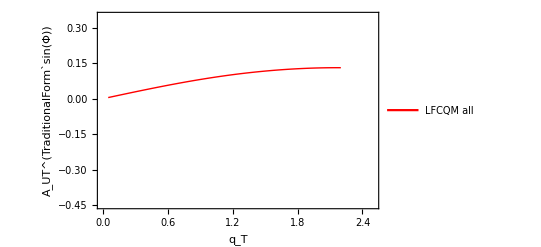

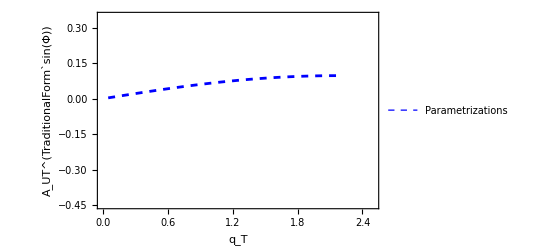

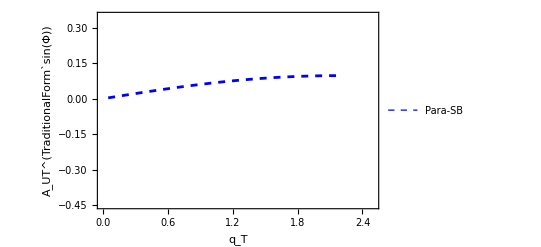

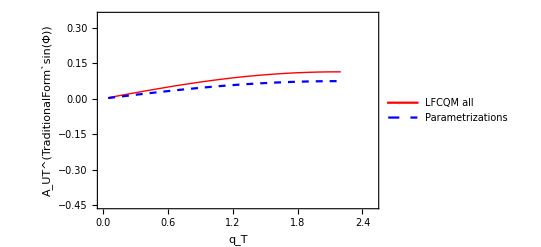

```mathematica
plotBarbAUT1qTa=Plot[shortBarbAUT1qTa[qT],{qT,0.05,2.2},PlotRange-> {{0,2.5},{-0.45,0.35}},Frame->True,FrameLabel->{"q_T","A_UT^(TraditionalForm`sin(Φ))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Red,Thick}},PlotLegends->Placed[{Style["LFCQM all",9.5]},{.75,.25}]]

plotAUT1qTa=Plot[shortAUT1qTa[qT],{qT,0.05,2.2},PlotRange-> {{0,2.5},{-0.45,0.35}},Frame->True,FrameLabel->{"q_T","A_UT^(TraditionalForm`sin(Φ))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Blue,Dashed,Thickness[0.005]}},PlotLegends->Placed[{Style["Parametrizations",9.5]},{.75,.15}]]
(* For legend adjustment: *)
plotAUT1qTa2=Plot[shortAUT1qTa[qT],{qT,0.05,2.2},PlotRange-> {{0,2.5},{-0.45,0.35}},Frame->True,FrameLabel->{"q_T","A_UT^(TraditionalForm`sin(Φ))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Blue,Dashed,Thickness[0.005]}},PlotLegends->Placed[{Style["Para-SB",9.5]},{.75,.25}]]

(**** Interpolation trick is done to save time  ****)
plotAUT1qTb=Plot[{shortBarbAUT1qTb[qT],shortAUT1qTb[qT]},{qT,0.05,2.2},PlotRange-> {{0,2.5},{-0.45,0.35}},Frame->True,FrameLabel->{"q_T","A_UT^(TraditionalForm`sin(Φ))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Red,Thick},{Blue,Dashed}},PlotLegends->Placed[{Style["LFCQM all",9.5],Style["Parametrizations",9.5]},{.25,.2}]]
```

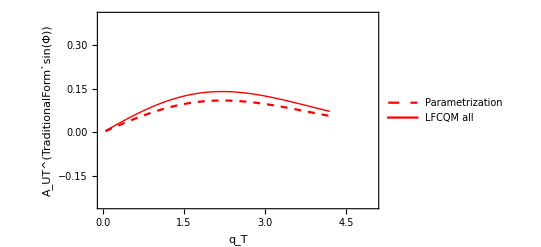

```mathematica
plotAUT1qTnaive=Plot[{AUT1[0.5,0.17,28,qT],BarbAUT1[0.5,0.17,28,qT]},{qT,0.05,4.2},PlotRange-> {{0,5},{-0.25,0.4}},Frame->True,FrameLabel->{"q_T","A_UT^(TraditionalForm`sin(Φ))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Red,Dashed},{Red,Thick}},PlotLegends->Placed[{Style["Parametrization",8],Style["LFCQM all",8]},{.8,.8}]]
```

#### Experimental Plots

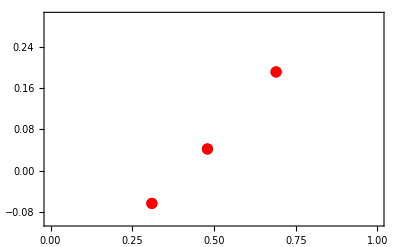

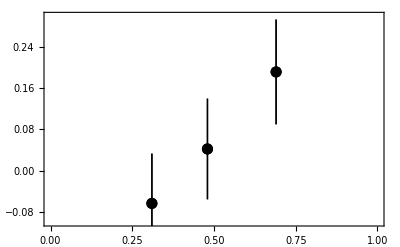

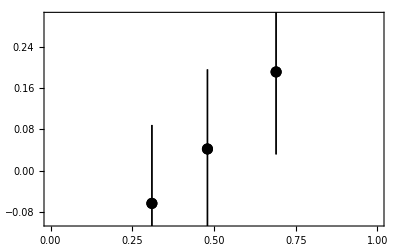

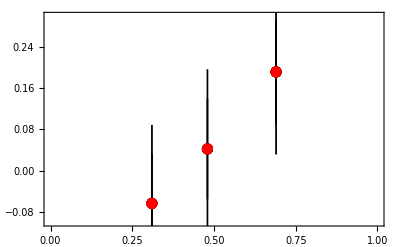

```mathematica
(********************************************************)
Clear[data,tab];
data=Cases[Import["./data/A_T_sin_phiS_x_pi.dat","Table"],{_?NumberQ,___}]; 
tabpoints =  Table[{{data[[i]][[4]],data[[i]][[8]]}},{i,Length[data]}];
tab =  Table[{{data[[i]][[4]],data[[i]][[8]]},ErrorBar[data[[i]][[9]]]},{i,Length[data]},{j,1}];
tabsys =  Table[{{data[[i]][[4]],data[[i]][[8]]},ErrorBar[Sqrt[data[[i]][[9]]^2+data[[i]][[10]]^2]]},{i,Length[data]},{j,1}];

plotdataCOMPASSpimPoints=ListPlot[tabpoints, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpimsys=ErrorListPlot[tabsys, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdata1xa = Show[plotdataCOMPASSpim, plotdataCOMPASSpimsys,plotdataCOMPASSpimPoints]
```

```mathematica
(***************************************************************)
```

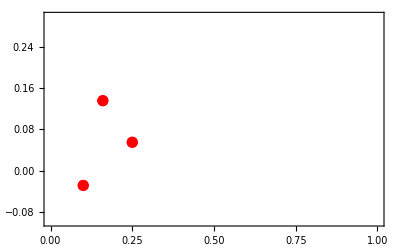

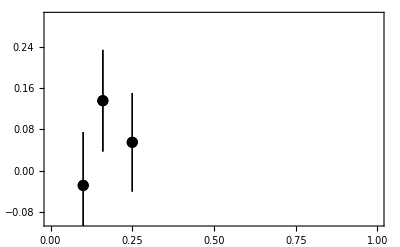

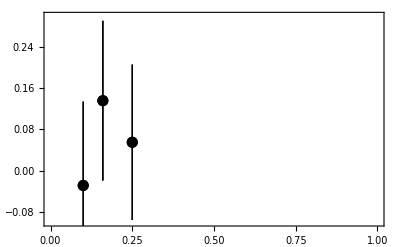

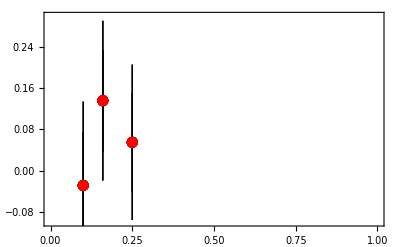

```mathematica
Clear[data,tab];
data=Cases[Import["./data/A_T_sin_phiS_x_N.dat","Table"],{_?NumberQ,___}]; 
tabpoints =  Table[{{data[[i]][[3]],data[[i]][[8]]}},{i,Length[data]}];
tab =  Table[{{data[[i]][[3]],data[[i]][[8]]},ErrorBar[data[[i]][[9]]]},{i,Length[data]},{j,1}];
tabsys =  Table[{{data[[i]][[3]],data[[i]][[8]]},ErrorBar[Sqrt[data[[i]][[9]]^2+data[[i]][[10]]^2]]},{i,Length[data]},{j,1}];
plotdataCOMPASSpimPoints=ListPlot[tabpoints, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpimsys=ErrorListPlot[tabsys, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdata1xb = Show[plotdataCOMPASSpim, plotdataCOMPASSpimsys,plotdataCOMPASSpimPoints]
```

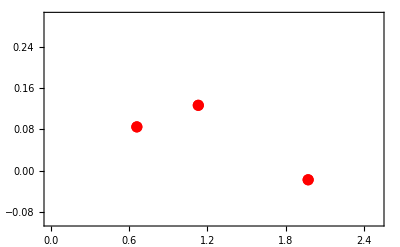

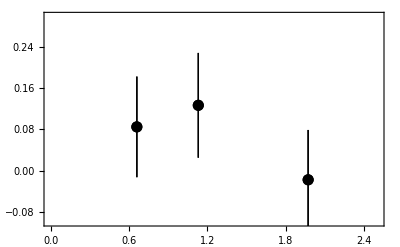

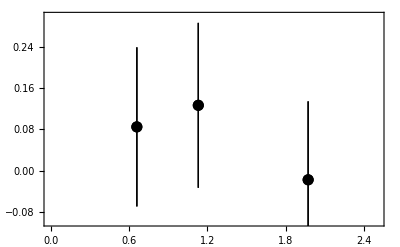

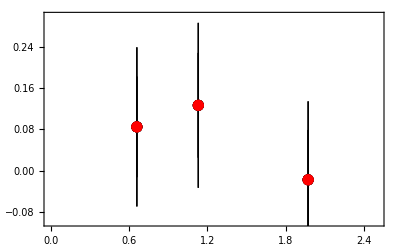

```mathematica
(*****************************************************************)
Clear[data,tab];
data=Cases[Import["./data/A_T_sin_phiS_q_T.dat","Table"],{_?NumberQ,___}]; 
tabpoints =  Table[{{data[[i]][[6]],data[[i]][[8]]}},{i,Length[data]}];
tab =  Table[{{data[[i]][[6]],data[[i]][[8]]},ErrorBar[data[[i]][[9]]]},{i,Length[data]},{j,1}];
tabsys =  Table[{{data[[i]][[6]],data[[i]][[8]]},ErrorBar[Sqrt[data[[i]][[9]]^2+data[[i]][[10]]^2]]},{i,Length[data]},{j,1}];
plotdataCOMPASSpimPoints=ListPlot[tabpoints, Frame-> True,PlotRange->{{0,2.5},{-0.1,0.3}}, PlotStyle->{{Red,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,2.5},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpimsys=ErrorListPlot[tabsys, Frame-> True,PlotRange->{{0,2.5},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdata1qT = Show[plotdataCOMPASSpim, plotdataCOMPASSpimsys,plotdataCOMPASSpimPoints]
```

#### Final Plots

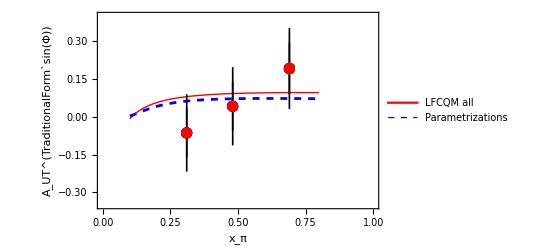

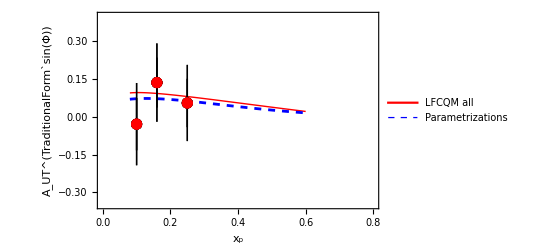

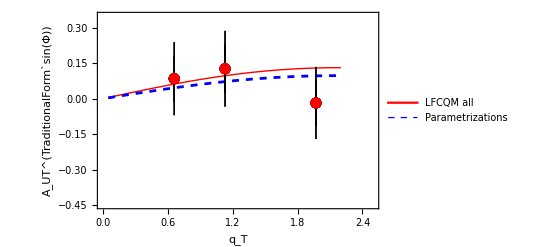

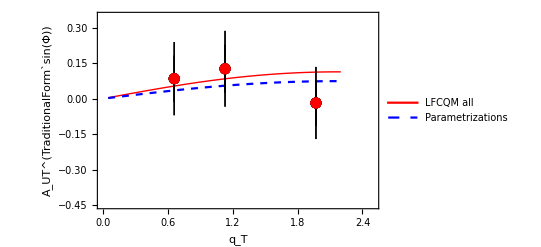

```mathematica
(********************  Final Plots for Subscript[A, UT]^(sinϕ)) *****************************)
Show[plotBarbAUT1xa,plotAUT1xa,plotdata1xa]
Show[plotBarbAUT1xb,plotAUT1xb,plotdata1xb]
Show[plotBarbAUT1qTa,plotAUT1qTa,plotdata1qT]
Show[plotAUT1qTb,plotdata1qT]
```

### A_UT^(sin(2Φ-Φ_b))

#### Numerical Calculations

Di-quark hybrid

```mathematica
(* BM from di-quark and the rest from parametrizations *)

DQhybridAUTsin2ϕmϕb[xa_,xb_,Q2_,qT_]:=DQhybridFUTsin2ϕmϕb[xa,xb,Q2,qT]/FUU1[xa,xb,Q2,qT]


DQhybridAUTsin2ϕmϕbqint[xa_,xb_,Q2_]:=DQhybridFUTsin2ϕmϕbqint[xa,xb,Q2]/FUU1qint[xa,xb,Q2]


DQhybridAUTsin2ϕmϕbqTa[Q2_,qT_]:=DQhybridFUTsin2ϕmϕbqTa[Q2,qT]/FUU1qTa[Q2,qT]
DisDQhybridAUTsin2ϕmϕbqTa[Q2_,step_]:=Table[{qT,DQhybridAUTsin2ϕmϕbqTa[Q2,qT]},{qT,.02,2.2,step}]


DQhybridAUTsin2ϕmϕbqTb[Q2_,qT_]:=DQhybridFUTsin2ϕmϕbqTb[Q2,qT]/FUU1qTb[Q2,qT]
DisDQhybridAUTsin2ϕmϕbqTb[Q2_,step_]:=Table[{qT,DQhybridAUTsin2ϕmϕbqTb[Q2,qT]},{qT,.02,2.2,step}]



DQhybridFUTsin2ϕmϕb[xa_,xb_,Q2_,qT_]:=-(2 Ma)/(π qw["BM","T"]^2)qT  ⅇ^(-qT^2/qw["BM","T"])   ∑_(q=1)^3 Subscript[e, q]^2(OverBar[Subscript[DQh1p1a, q]][xa,Q2] Subscript[h1b, q][xb,Q2]+OverBar[Subscript[h1b, q]][xb,Q2] Subscript[DQh1p1a, q][xa,Q2])


DQhybridFUTsin2ϕmϕbqint[xa_,xb_,Q2_]:=-(√π Ma)/(√qw["BM","T"])   ∑_(q=1)^3 Subscript[e, q]^2(OverBar[Subscript[DQh1p1a, q]][xa,Q2] Subscript[h1b, q][xb,Q2]+OverBar[Subscript[h1b, q]][xb,Q2] Subscript[DQh1p1a, q][xa,Q2])


DQhybridFUTsin2ϕmϕbqTa[Q2_,qT_]:=NIntegrate[DQhybridFUTsin2ϕmϕb[xa,Q2/(xa stot),Q2,qT],{xa,Q2/stot,.9}]
DQhybridFUTsin2ϕmϕbqTb[Q2_,qT_]:=NIntegrate[DQhybridFUTsin2ϕmϕb[Q2/(xb stot),xb,Q2,qT],{xb,Q2/stot,.9}]



Subscript[h1b, 1][xb_,Q2_]:=h1u[xb,Q2];Subscript[h1b, 2][xb_,Q2_]:=h1d[xb,Q2];Subscript[h1b, 3][xb_,Q2_]:=0
OverBar[Subscript[h1b, 1]][xb_,Q2_]:=0;OverBar[Subscript[h1b, 2]][xb_,Q2_]:=0;OverBar[Subscript[h1b, 3]][xb_,Q2_]:=0
Subscript[DQh1p1a, 1][xa_,Q2_]:=0;Subscript[DQh1p1a, 2][xa_,Q2_]:=Leoh1p1π[xa,Q2] ;Subscript[DQh1p1a, 3][xa_,Q2_]:=0
OverBar[Subscript[DQh1p1a, 1]][xa_,Q2_]:=Leoh1p1π[xa,Q2];OverBar[Subscript[DQh1p1a, 2]][xa_,Q2_]:=0 ;OverBar[Subscript[DQh1p1a, 3]][xa_,Q2_]:=0
```

LFCQM hybrid

```mathematica
(* Only BM from LFCQM and the rest from parametrizations *)

LFChybridAUTsin2ϕmϕb[xa_,xb_,Q2_,qT_]:=LFChybridFUTsin2ϕmϕb[xa,xb,Q2,qT]/FUU1[xa,xb,Q2,qT]


LFChybridAUTsin2ϕmϕbqint[xa_,xb_,Q2_]:=LFChybridFUTsin2ϕmϕbqint[xa,xb,Q2]/FUU1qint[xa,xb,Q2]


LFChybridAUTsin2ϕmϕbqTa[Q2_,qT_]:=LFChybridFUTsin2ϕmϕbqTa[Q2,qT]/FUU1qTa[Q2,qT]
DisLFChybridAUTsin2ϕmϕbqTa[Q2_,step_]:=Table[{qT,LFChybridAUTsin2ϕmϕbqTa[Q2,qT]},{qT,.02,2.2,step}]


LFChybridAUTsin2ϕmϕbqTb[Q2_,qT_]:=LFChybridFUTsin2ϕmϕbqTb[Q2,qT]/FUU1qTb[Q2,qT]
DisLFChybridAUTsin2ϕmϕbqTb[Q2_,step_]:=Table[{qT,LFChybridAUTsin2ϕmϕbqTb[Q2,qT]},{qT,.02,2.2,step}]


LFChybridFUTsin2ϕmϕb[xa_,xb_,Q2_,qT_]:=-(2 Ma)/(π qw["BM","T"]^2)qT  ⅇ^(-qT^2/qw["BM","T"])   ∑_(q=1)^3 Subscript[e, q]^2(OverBar[Subscript[Bh1p1a, q]][xa,Q2] Subscript[h1b, q][xb,Q2]+OverBar[Subscript[h1b, q]][xb,Q2] Subscript[Bh1p1a, q][xa,Q2])

LFChybridFUTsin2ϕmϕbqint[xa_,xb_,Q2_]:=-(√π Ma)/(√qw["BM","T"])   ∑_(q=1)^3 Subscript[e, q]^2(OverBar[Subscript[Bh1p1a, q]][xa,Q2] Subscript[h1b, q][xb,Q2]+OverBar[Subscript[h1b, q]][xb,Q2] Subscript[Bh1p1a, q][xa,Q2])


LFChybridFUTsin2ϕmϕbqTa[Q2_,qT_]:=NIntegrate[LFChybridFUTsin2ϕmϕb[xa,Q2/(xa stot),Q2,qT],{xa,Q2/stot,.9}]
LFChybridFUTsin2ϕmϕbqTb[Q2_,qT_]:=NIntegrate[LFChybridFUTsin2ϕmϕb[Q2/(xb stot),xb,Q2,qT],{xb,Q2/stot,.9}]



Subscript[h1b, 1][xb_,Q2_]:=h1u[xb,Q2];Subscript[h1b, 2][xb_,Q2_]:=h1d[xb,Q2];Subscript[h1b, 3][xb_,Q2_]:=0
OverBar[Subscript[h1b, 1]][xb_,Q2_]:=0;OverBar[Subscript[h1b, 2]][xb_,Q2_]:=0;OverBar[Subscript[h1b, 3]][xb_,Q2_]:=0
Subscript[Bh1p1a, 1][xa_,Q2_]:=0;Subscript[Bh1p1a, 2][xa_,Q2_]:=Barbxh1perp1uπ[xa]/xa ;Subscript[Bh1p1a, 3][xa_,Q2_]:=0
OverBar[Subscript[Bh1p1a, 1]][xa_,Q2_]:=Barbxh1perp1uπ[xa]/xa ;OverBar[Subscript[Bh1p1a, 2]][xa_,Q2_]:=0 ;OverBar[Subscript[Bh1p1a, 3]][xa_,Q2_]:=0
```

LFCQM all

```mathematica
(*** All inputs from Barbara's LFCQM ***)

BarbAUTsin2ϕmϕb[xa_,xb_,Q2_,qT_]:=BarbFUTsin2ϕmϕb[xa,xb,Q2,qT]/BarbFUU1[xa,xb,Q2,qT]


BarbAUTsin2ϕmϕbqint[xa_,xb_,Q2_]:=BarbFUTsin2ϕmϕbqint[xa,xb,Q2]/BarbFUU1qint[xa,xb,Q2]


BarbAUTsin2ϕmϕbqTa[Q2_,qT_]:=BarbFUTsin2ϕmϕbqTa[Q2,qT]/BarbFUU1qTa[Q2,qT]
DisBarbAUTsin2ϕmϕbqTa[Q2_,step_]:=Table[{qT,BarbAUTsin2ϕmϕbqTa[Q2,qT]},{qT,.02,2.2,step}]


BarbAUTsin2ϕmϕbqTb[Q2_,qT_]:=BarbFUTsin2ϕmϕbqTb[Q2,qT]/BarbFUU1qTb[Q2,qT]
DisBarbAUTsin2ϕmϕbqTb[Q2_,step_]:=Table[{qT,BarbAUTsin2ϕmϕbqTb[Q2,qT]},{qT,.02,2.2,step}]


BarbFUTsin2ϕmϕb[xa_,xb_,Q2_,qT_]:=-(2 Ma  qT ⅇ^(-qT^2/qw["BM","T"]))/(π qw["BM","T"]^2)   ∑_(q=1)^2 Subscript[e, q]^2(OverBar[Subscript[Bh1p1a, q]][xa,Q2] Subscript[Bh1b, q][xb,Q2]+OverBar[Subscript[Bh1b, q]][xb,Q2] Subscript[Bh1p1a, q][xa,Q2])

BarbFUTsin2ϕmϕbqint[xa_,xb_,Q2_]:=-(√π Ma)/(√qw["BM","T"])   ∑_(q=1)^2 Subscript[e, q]^2(OverBar[Subscript[Bh1p1a, q]][xa,Q2] Subscript[Bh1b, q][xb,Q2]+OverBar[Subscript[Bh1b, q]][xb,Q2] Subscript[Bh1p1a, q][xa,Q2])


BarbFUTsin2ϕmϕbqTa[Q2_,qT_]:=NIntegrate[BarbFUTsin2ϕmϕb[xa,Q2/(xa stot),Q2,qT],{xa,Q2/stot,.9}]
BarbFUTsin2ϕmϕbqTb[Q2_,qT_]:=NIntegrate[BarbFUTsin2ϕmϕb[Q2/(xb stot),xb,Q2,qT],{xb,Q2/stot,.9}]



Subscript[Bh1p1a, 1][x_,Q2_]:=0;Subscript[Bh1p1a, 2][x_,Q2_]:=Barbxh1perp1uπ[x]/x;
OverBar[Subscript[Bh1p1a, 1]][x_,Q2_]:=Barbxh1perp1uπ[x]/x ;OverBar[Subscript[Bh1p1a, 2]][x_,Q2_]:=0 ;
Subscript[Bh1b, 1][x_,Q2_]:=Barbxh1u[x]/x;Subscript[Bh1b, 2][x_,Q2_]:=Barbxh1d[x]/x;
OverBar[Subscript[Bh1b, 1]][x_,Q2_]:=0;OverBar[Subscript[Bh1b, 2]][x_,Q2_]:=0;
```

#### Theoretical Plots

x_π-dependent

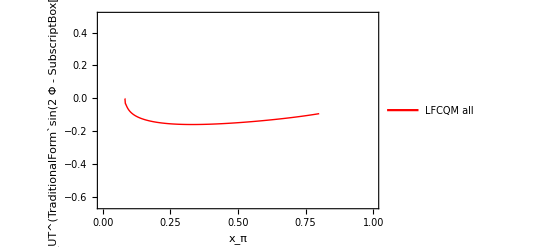

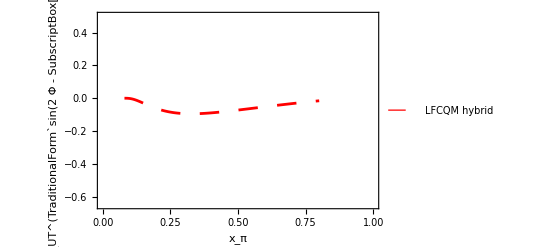

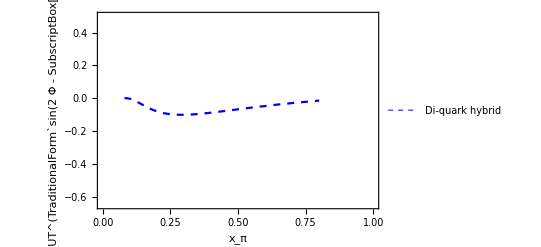

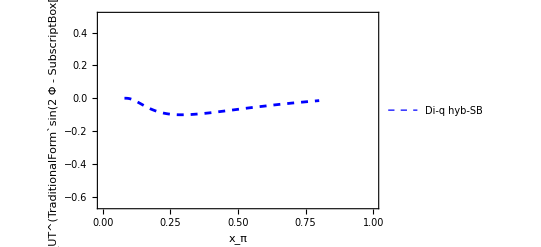

```mathematica
plotBarbAUTsin2ϕmϕbxa=Plot[BarbAUTsin2ϕmϕbqint[xa,28/(xa stot),28],{xa,0.081,0.8},PlotRange->{{0,1},{-.65,.5}},Frame->True,FrameLabel->{"x_π","A_UT^(TraditionalForm`sin(2  Φ - SubscriptBox[Φ, b]))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Red,Thick},{Red,Dashed}},PlotLegends->Placed[{Style["LFCQM all",9.5]},{.25,.9}]]

plotLFChybridAUTsin2ϕmϕbxa=Plot[LFChybridAUTsin2ϕmϕbqint[xa,28/(xa stot),28],{xa,0.0801,0.8},PlotRange->{{0,1},{-.65,.5}},Frame->True,FrameLabel->{"x_π","A_UT^(TraditionalForm`sin(2  Φ - SubscriptBox[Φ, b]))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Red,Dashing[Large],Thickness[0.005]}},PlotLegends->Placed[{Style["LFCQM hybrid",9.5]},{.25,.8}]]

plotDQhybridAUTsin2ϕmϕbxa=Plot[DQhybridAUTsin2ϕmϕbqint[xa,28/(xa stot),28],{xa,0.0801,0.8},PlotRange->{{0,1},{-.65,.5}},Frame->True,FrameLabel->{"x_π","A_UT^(TraditionalForm`sin(2  Φ - SubscriptBox[Φ, b]))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Blue,Dashed,Thickness[0.004]}},PlotLegends->Placed[{Style["Di-quark hybrid",9.5]},{.25,.7}]]
(* For legend adjustment : *)
plotDQhybridAUTsin2ϕmϕbxa2=Plot[DQhybridAUTsin2ϕmϕbqint[xa,28/(xa stot),28],{xa,0.0801,0.8},PlotRange->{{0,1},{-.65,.5}},Frame->True,FrameLabel->{"x_π","A_UT^(TraditionalForm`sin(2  Φ - SubscriptBox[Φ, b]))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Blue,Dashed,Thickness[0.005]}},PlotLegends->Placed[{Style["Di-q hyb-SB",9.5]},{.25,.85}]]
```

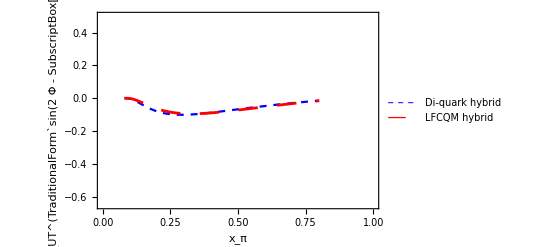

```mathematica
Show[plotDQhybridAUTsin2ϕmϕbxa,plotLFChybridAUTsin2ϕmϕbxa]
```

x_p-dependent

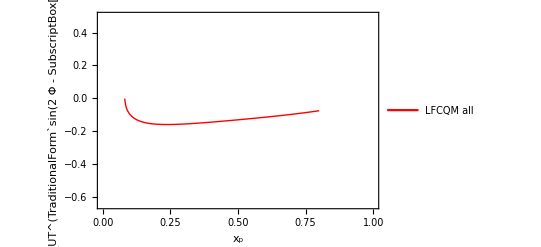

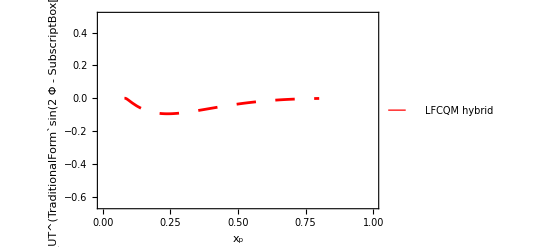

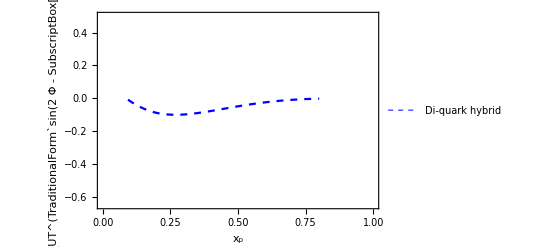

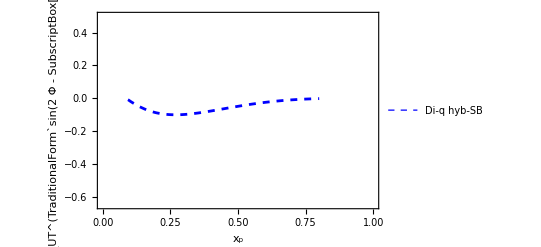

```mathematica
plotBarbAUTsin2ϕmϕbxb=Plot[BarbAUTsin2ϕmϕbqint[28/(xb stot),xb,28],{xb,0.081,0.8},PlotRange->{{0,1},{-.65,.5}},Frame->True,FrameLabel->{"x_p","A_UT^(TraditionalForm`sin(2  Φ - SubscriptBox[Φ, b]))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Red,Thick},{Red,Dashed}},PlotLegends->Placed[{Style["LFCQM all",9.5]},{.75,.9}]]

plotLFChybridAUTsin2ϕmϕbxb=Plot[LFChybridAUTsin2ϕmϕbqint[28/(xb stot),xb,28],{xb,0.0801,0.8},PlotRange->{{0,1},{-.65,.5}},Frame->True,FrameLabel->{"x_p","A_UT^(TraditionalForm`sin(2  Φ - SubscriptBox[Φ, b]))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Red,Dashing[Large],Thickness[0.005]}},PlotLegends->Placed[{Style["LFCQM hybrid",9.5]},{.75,.8}]]

plotDQhybridAUTsin2ϕmϕbxb=Plot[DQhybridAUTsin2ϕmϕbqint[28/(xb stot),xb,28],{xb,0.093,0.8},PlotRange->{{0,1},{-.65,.5}},Frame->True,FrameLabel->{"x_p","A_UT^(TraditionalForm`sin(2  Φ - SubscriptBox[Φ, b]))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Blue,Dashed,Thickness[0.004]}},PlotLegends->Placed[{Style["Di-quark hybrid",9.5]},{.75,.7}]]
(* Legend adjustment : *) 
plotDQhybridAUTsin2ϕmϕbxb2=Plot[DQhybridAUTsin2ϕmϕbqint[28/(xb stot),xb,28],{xb,0.093,0.8},PlotRange->{{0,1},{-.65,.5}},Frame->True,FrameLabel->{"x_p","A_UT^(TraditionalForm`sin(2  Φ - SubscriptBox[Φ, b]))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Blue,Dashed,Thickness[0.005]}},PlotLegends->Placed[{Style["Di-q hyb-SB",9.5]},{.75,.85}]]
```

q_T-dependent

```mathematica
(** qT dependence with integration over xa  **)
shortDQhybridAUTsin2ϕmϕbqTa=Interpolation[DisDQhybridAUTsin2ϕmϕbqTa[28,.2]];
shortLFChybridAUTsin2ϕmϕbqTa=Interpolation[DisLFChybridAUTsin2ϕmϕbqTa[28,.2]];
shortBarbAUTsin2ϕmϕbqTa=Interpolation[DisBarbAUTsin2ϕmϕbqTa[28,.2]];


(** qT dependence with integration over xb  **)
shortDQhybridAUTsin2ϕmϕbqTb=Interpolation[DisDQhybridAUTsin2ϕmϕbqTb[28,.2]];
shortLFChybridAUTsin2ϕmϕbqTb=Interpolation[DisLFChybridAUTsin2ϕmϕbqTb[28,.2]];
shortBarbAUTsin2ϕmϕbqTb=Interpolation[DisBarbAUTsin2ϕmϕbqTb[28,.2]];
```

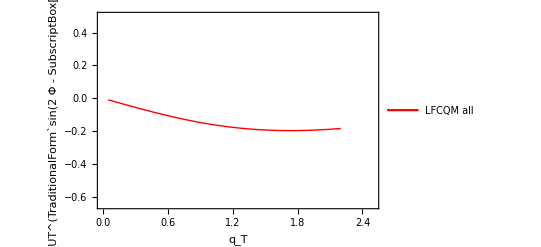

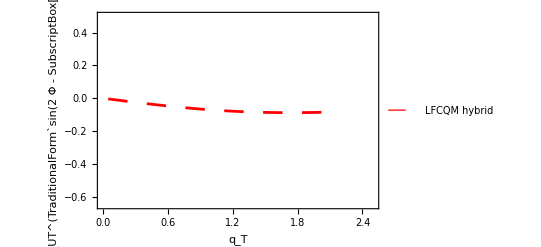

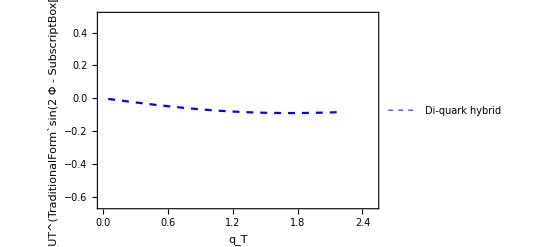

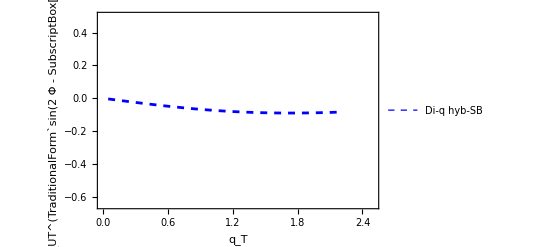

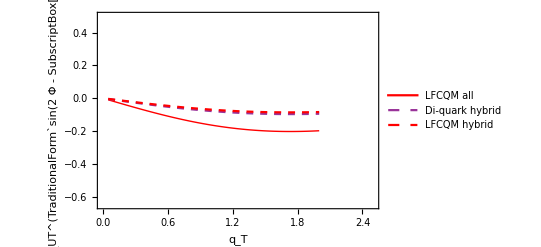

```mathematica
plotBarbAUTsin2ϕmϕbqTa=Plot[shortBarbAUTsin2ϕmϕbqTa[qT],{qT,0.05,2.2},PlotRange->{{0,2.5},{-.65,.5}},Frame->True,FrameLabel->{"q_T","A_UT^(TraditionalForm`sin(2  Φ - SubscriptBox[Φ, b]))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Red,Thick}},PlotLegends->Placed[{Style["LFCQM all",9.5]},{.25,.9}]]


plotLFChybridAUTsin2ϕmϕbqTa=Plot[shortLFChybridAUTsin2ϕmϕbqTa[qT],{qT,0.05,2.2},PlotRange->{{0,2.5},{-.65,.5}},Frame->True,FrameLabel->{"q_T","A_UT^(TraditionalForm`sin(2  Φ - SubscriptBox[Φ, b]))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Red,Dashing[Large],Thickness[0.005]}},PlotLegends->Placed[{Style["LFCQM hybrid",9.5]},{.25,.8}]]


plotDQhybridAUTsin2ϕmϕbqTa=Plot[shortDQhybridAUTsin2ϕmϕbqTa[qT],{qT,0.05,2.2},PlotRange->{{0,2.5},{-.65,.5}},Frame->True,FrameLabel->{"q_T","A_UT^(TraditionalForm`sin(2  Φ - SubscriptBox[Φ, b]))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Blue,Dashed,Thickness[0.004]}},PlotLegends->Placed[{Style["Di-quark hybrid",9.5]},{.25,.7}]]
(* Legend adjustment *)
plotDQhybridAUTsin2ϕmϕbqTa2=Plot[shortDQhybridAUTsin2ϕmϕbqTa[qT],{qT,0.05,2.2},PlotRange->{{0,2.5},{-.65,.5}},Frame->True,FrameLabel->{"q_T","A_UT^(TraditionalForm`sin(2  Φ - SubscriptBox[Φ, b]))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Blue,Dashed,Thickness[0.005]}},PlotLegends->Placed[{Style["Di-q hyb-SB",9.5]},{.25,.85}]]



plotAUTsin2ϕmϕbqTb=Plot[{shortBarbAUTsin2ϕmϕbqTb[qT],shortDQhybridAUTsin2ϕmϕbqTb[qT],shortLFChybridAUTsin2ϕmϕbqTb[qT]},{qT,0.05,2.0},PlotRange->{{0,2.5},{-.65,.5}},Frame->True,FrameLabel->{"q_T","A_UT^(TraditionalForm`sin(2  Φ - SubscriptBox[Φ, b]))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Red,Thick},{Lighter[Purple,0.2],Dashed},{Red,Dashed}},PlotLegends->Placed[{Style["LFCQM all",10],Style["Di-quark hybrid",9.5],Style["LFCQM hybrid",9.5]},{.25,.8}]]
```

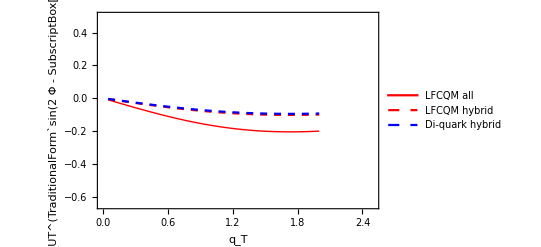

```mathematica
plotAUTsin2ϕmϕbqTnaive=Plot[{BarbAUTsin2ϕmϕb[0.5,0.17,28,qT],LFChybridAUTsin2ϕmϕb[0.5,0.17,28,qT],DQhybridAUTsin2ϕmϕb[0.5,0.17,28,qT]},{qT,0.05,2.0},PlotRange->{{0,2.5},{-.65,.5}},Frame->True,FrameLabel->{"q_T","A_UT^(TraditionalForm`sin(2  Φ - SubscriptBox[Φ, b]))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Red,Thick},{Red,Dashed},{Blue,Dashed}},PlotLegends->Placed[{Style["LFCQM all",9.5],Style["LFCQM hybrid",9.5],Style["Di-quark hybrid",9.5]},{.25,.8}]]
```

#### Experimental Plots

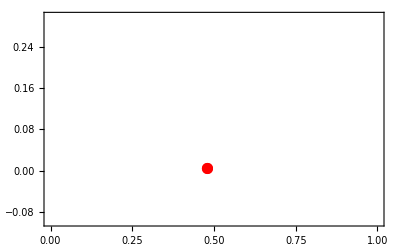

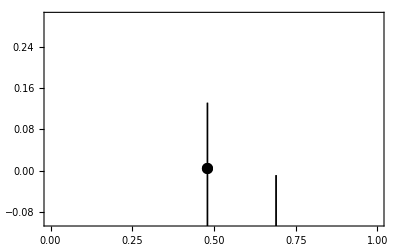

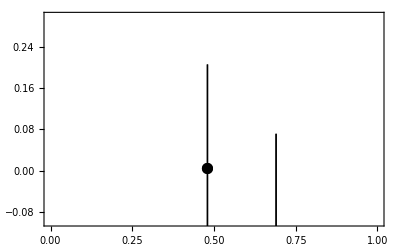

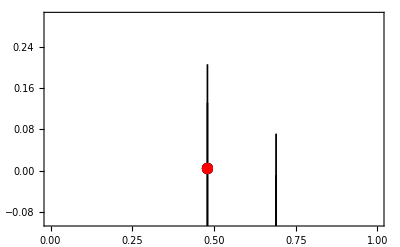

```mathematica
Clear[data,tab];
data=Cases[Import["./data/A_T_sin_2phiCS_m_phiS_x_pi.dat","Table"],{_?NumberQ,___}]; 
tabpoints =  Table[{{data[[i]][[4]],data[[i]][[8]]}},{i,Length[data]}];
tab =  Table[{{data[[i]][[4]],data[[i]][[8]]},ErrorBar[data[[i]][[9]]]},{i,Length[data]},{j,1}];
tabsys =  Table[{{data[[i]][[4]],data[[i]][[8]]},ErrorBar[Sqrt[data[[i]][[9]]^2+data[[i]][[10]]^2]]},{i,Length[data]},{j,1}];
plotdataCOMPASSpimPoints=ListPlot[tabpoints, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpimsys=ErrorListPlot[tabsys, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdata2xa = Show[plotdataCOMPASSpim, plotdataCOMPASSpimsys,plotdataCOMPASSpimPoints]
```

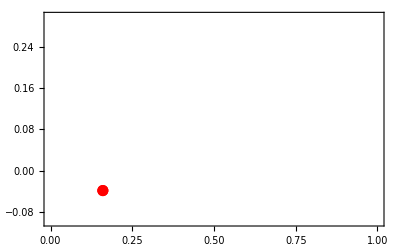

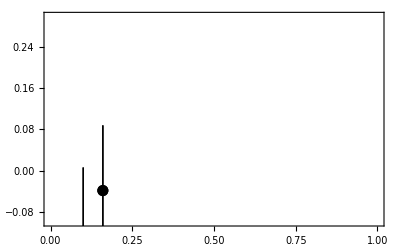

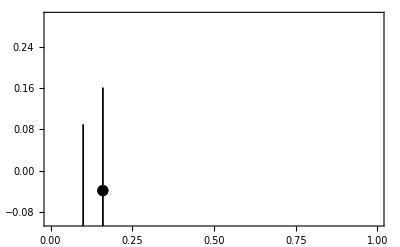

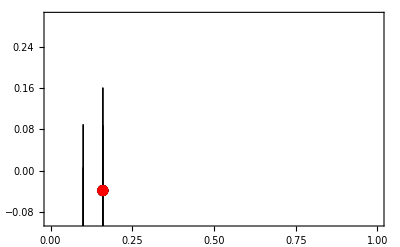

```mathematica
Clear[data,tab];
data=Cases[Import["./data/A_T_sin_2phiCS_m_phiS_x_N.dat","Table"],{_?NumberQ,___}]; 
tabpoints =  Table[{{data[[i]][[3]],data[[i]][[8]]}},{i,Length[data]}];
tab =  Table[{{data[[i]][[3]],data[[i]][[8]]},ErrorBar[data[[i]][[9]]]},{i,Length[data]},{j,1}];
tabsys =  Table[{{data[[i]][[3]],data[[i]][[8]]},ErrorBar[Sqrt[data[[i]][[9]]^2+data[[i]][[10]]^2]]},{i,Length[data]},{j,1}];
plotdataCOMPASSpimPoints=ListPlot[tabpoints, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpimsys=ErrorListPlot[tabsys, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdata2xb = Show[plotdataCOMPASSpim, plotdataCOMPASSpimsys,plotdataCOMPASSpimPoints]
```

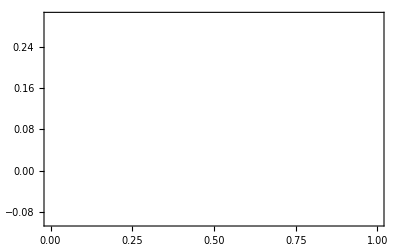

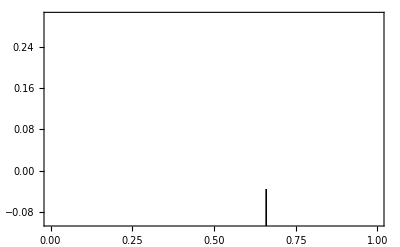

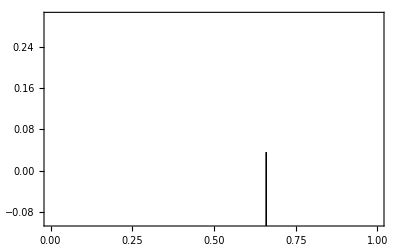

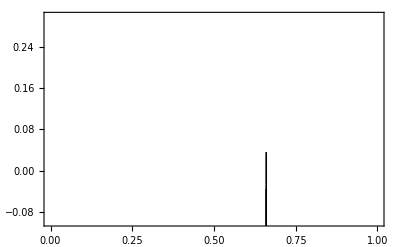

```mathematica
Clear[data,tab];
data=Cases[Import["./data/A_T_sin_2phiCS_m_phiS_q_T.dat","Table"],{_?NumberQ,___}]; 
tabpoints =  Table[{{data[[i]][[6]],data[[i]][[8]]}},{i,Length[data]}];
tab =  Table[{{data[[i]][[6]],data[[i]][[8]]},ErrorBar[data[[i]][[9]]]},{i,Length[data]},{j,1}];
tabsys =  Table[{{data[[i]][[6]],data[[i]][[8]]},ErrorBar[Sqrt[data[[i]][[9]]^2+data[[i]][[10]]^2]]},{i,Length[data]},{j,1}];
plotdataCOMPASSpimPoints=ListPlot[tabpoints, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpimsys=ErrorListPlot[tabsys, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdata2qT = Show[plotdataCOMPASSpim, plotdataCOMPASSpimsys,plotdataCOMPASSpimPoints]
```

#### Final Plots

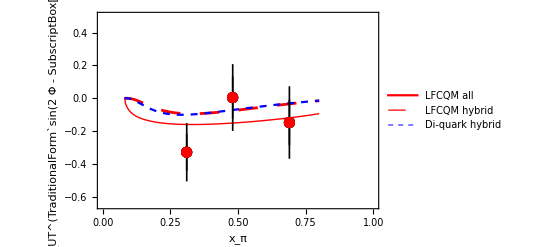

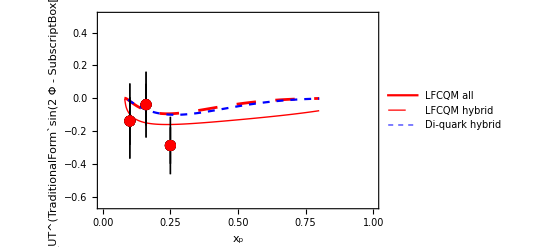

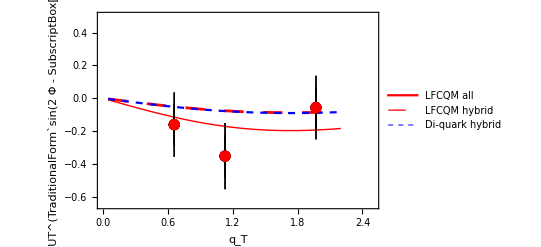

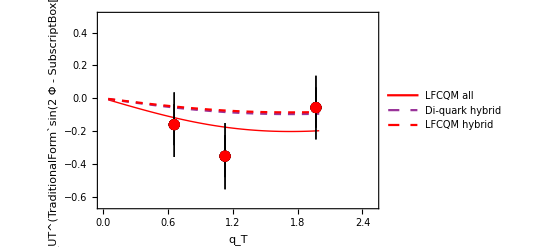

```mathematica
Show[plotBarbAUTsin2ϕmϕbxa,plotLFChybridAUTsin2ϕmϕbxa,plotDQhybridAUTsin2ϕmϕbxa,plotdata2xa]
Show[plotBarbAUTsin2ϕmϕbxb,plotLFChybridAUTsin2ϕmϕbxb,plotDQhybridAUTsin2ϕmϕbxb,plotdata2xb]
Show[plotBarbAUTsin2ϕmϕbqTa,plotLFChybridAUTsin2ϕmϕbqTa,plotDQhybridAUTsin2ϕmϕbqTa,plotdata2qT]
Show[plotAUTsin2ϕmϕbqTb,plotdata2qT]
```

### A_UT^(sin(2Φ+Φ_b))

#### Numerical Calculations

Di-quark hybrid

```mathematica
(** BM from Di-quark model and the rest from oarametrizations  **)

DQhybridAUTsin2ϕpϕb[xa_,xb_,Q2_,qT_]:=DQhybridFUTsin2ϕpϕb[xa,xb,Q2,qT]/FUU1[xa,xb,Q2,qT]


DQhybridAUTsin2ϕpϕbqint[xa_,xb_,Q2_]:=DQhybridFUTsin2ϕpϕbqint[xa,xb,Q2]/FUU1qint[xa,xb,Q2]


DQhybridAUTsin2ϕpϕbqTa[Q2_,qT_]:=DQhybridFUTsin2ϕpϕbqTa[Q2,qT]/FUU1qTa[Q2,qT]
DisDQhybridAUTsin2ϕpϕbqTa[Q2_,step_]:=Table[{qT,DQhybridAUTsin2ϕpϕbqTa[Q2,qT]},{qT,.02,2.2,step}]


DQhybridAUTsin2ϕpϕbqTb[Q2_,qT_]:=DQhybridFUTsin2ϕpϕbqTb[Q2,qT]/FUU1qTb[Q2,qT]
DisDQhybridAUTsin2ϕpϕbqTb[Q2_,step_]:=Table[{qT,DQhybridAUTsin2ϕpϕbqTb[Q2,qT]},{qT,.02,2.2,step}]



DQhybridFUTsin2ϕpϕb[xa_,xb_,Q2_,qT_]:=-(2 Ma  Mb^2)/(π qw["BM","P"]^4)qT^3  ⅇ^(-qT^2/qw["BM","P"])   ∑_(q=1)^3 Subscript[e, q]^2(OverBar[Subscript[DQh1p1a, q]][xa,Q2] Subscript[h1Tp2b, q][xb,Q2]+OverBar[Subscript[h1Tp2b, q]][xb,Q2] Subscript[DQh1p1a, q][xa,Q2])

DQhybridFUTsin2ϕpϕbqint[xa_,xb_,Q2_]:=-(3 √π Ma  Mb^2)/(2 √(qw["BM","P"]^3))   ∑_(q=1)^3 Subscript[e, q]^2(OverBar[Subscript[DQh1p1a, q]][xa,Q2] Subscript[h1Tp2b, q][xb,Q2]+OverBar[Subscript[h1Tp2b, q]][xb,Q2] Subscript[DQh1p1a, q][xa,Q2])


DQhybridFUTsin2ϕpϕbqTa[Q2_,qT_]:=NIntegrate[DQhybridFUTsin2ϕpϕb[xa,Q2/(xa stot),Q2,qT],{xa,Q2/stot,.9}]
DQhybridFUTsin2ϕpϕbqTb[Q2_,qT_]:=NIntegrate[DQhybridFUTsin2ϕpϕb[Q2/(xb stot),xb,Q2,qT],{xb,Q2/stot,.9}]


Subscript[h1Tp2b, 1][xb_,Q2_]:=h1Tp2u[xb,Q2];Subscript[h1Tp2b, 2][xb_,Q2_]:=h1Tp2d[xb,Q2];Subscript[h1Tp2b, 3][xb_,Q2_]:=0;OverBar[Subscript[h1Tp2b, 1]][xb_,Q2_]:=0;OverBar[Subscript[h1Tp2b, 2]][xb_,Q2_]:=0;OverBar[Subscript[h1Tp2b, 3]][xb_,Q2_]:=0;
```

LFCQM hybrid

```mathematica
(** BM from Barbara and the rest from parametrizations *)

LFChybridAUTsin2ϕpϕb[xa_,xb_,Q2_,qT_]:=LFChybridFUTsin2ϕpϕb[xa,xb,Q2,qT]/FUU1[xa,xb,Q2,qT]


LFChybridAUTsin2ϕpϕbqint[xa_,xb_,Q2_]:=LFChybridFUTsin2ϕpϕbqint[xa,xb,Q2]/FUU1qint[xa,xb,Q2]


LFChybridAUTsin2ϕpϕbqTa[Q2_,qT_]:=LFChybridFUTsin2ϕpϕbqTa[Q2,qT]/FUU1qTa[Q2,qT]
DisLFChybridAUTsin2ϕpϕbqTa[Q2_,step_]:=Table[{qT,LFChybridAUTsin2ϕpϕbqTa[Q2,qT]},{qT,.02,2.2,step}]


LFChybridAUTsin2ϕpϕbqTb[Q2_,qT_]:=LFChybridFUTsin2ϕpϕbqTb[Q2,qT]/FUU1qTb[Q2,qT]
DisLFChybridAUTsin2ϕpϕbqTb[Q2_,step_]:=Table[{qT,LFChybridAUTsin2ϕpϕbqTb[Q2,qT]},{qT,.02,2.2,step}]


LFChybridFUTsin2ϕpϕb[xa_,xb_,Q2_,qT_]:=-(2 Ma  Mb^2)/(π qw["BM","P"]^4)qT^3  ⅇ^(-qT^2/qw["BM","P"])   ∑_(q=1)^3 Subscript[e, q]^2(OverBar[Subscript[Bh1p1a, q]][xa,Q2] Subscript[h1Tp2b, q][xb,Q2]+OverBar[Subscript[h1Tp2b, q]][xb,Q2] Subscript[Bh1p1a, q][xa,Q2])

LFChybridFUTsin2ϕpϕbqint[xa_,xb_,Q2_]:=-(3 √π Ma  Mb^2)/(2 √(qw["BM","P"]^3))   ∑_(q=1)^3 Subscript[e, q]^2(OverBar[Subscript[Bh1p1a, q]][xa,Q2] Subscript[h1Tp2b, q][xb,Q2]+OverBar[Subscript[h1Tp2b, q]][xb,Q2] Subscript[Bh1p1a, q][xa,Q2])


LFChybridFUTsin2ϕpϕbqTa[Q2_,qT_]:=NIntegrate[LFChybridFUTsin2ϕpϕb[xa,Q2/(xa stot),Q2,qT],{xa,Q2/stot,.9}]
LFChybridFUTsin2ϕpϕbqTb[Q2_,qT_]:=NIntegrate[LFChybridFUTsin2ϕpϕb[Q2/(xb stot),xb,Q2,qT],{xb,Q2/stot,.9}]
```

LFCQM all

```mathematica
(*** All inputs from Barbara's model **) 
BarbAUTsin2ϕpϕb[xa_,xb_,Q2_,qT_]:=BarbFUTsin2ϕpϕb[xa,xb,Q2,qT]/BarbFUU1[xa,xb,Q2,qT]


BarbAUTsin2ϕpϕbqint[xa_,xb_,Q2_]:=BarbFUTsin2ϕpϕbqint[xa,xb,Q2]/BarbFUU1qint[xa,xb,Q2]


BarbAUTsin2ϕpϕbqTa[Q2_,qT_]:=BarbFUTsin2ϕpϕbqTa[Q2,qT]/BarbFUU1qTa[Q2,qT]
DisBarbAUTsin2ϕpϕbqTa[Q2_,step_]:=Table[{qT,BarbAUTsin2ϕpϕbqTa[Q2,qT]},{qT,.02,2.2,step}]


BarbAUTsin2ϕpϕbqTb[Q2_,qT_]:=BarbFUTsin2ϕpϕbqTb[Q2,qT]/BarbFUU1qTb[Q2,qT]
DisBarbAUTsin2ϕpϕbqTb[Q2_,step_]:=Table[{qT,BarbAUTsin2ϕpϕbqTb[Q2,qT]},{qT,.02,2.2,step}]



BarbFUTsin2ϕpϕb[xa_,xb_,Q2_,qT_]:=-(2Ma  Mb^2)/(π qw["BM","P"]^4)qT^3 ⅇ^(-qT^2/qw["BM","P"])   ∑_(q=1)^2 Subscript[e, q]^2(OverBar[Subscript[Bh1p1a, q]][xa,Q2] Subscript[Bh1Tp2b, q][xb,Q2]+OverBar[Subscript[Bh1Tp2b, q]][xb,Q2] Subscript[Bh1p1a, q][xa,Q2])

BarbFUTsin2ϕpϕbqint[xa_,xb_,Q2_]:=-(3 √π Ma  Mb^2)/(2 √(qw["BM","P"]^3))    ∑_(q=1)^2 Subscript[e, q]^2(OverBar[Subscript[Bh1p1a, q]][xa,Q2] Subscript[Bh1Tp2b, q][xb,Q2]+OverBar[Subscript[Bh1Tp2b, q]][xb,Q2] Subscript[Bh1p1a, q][xa,Q2])


BarbFUTsin2ϕpϕbqTa[Q2_,qT_]:=NIntegrate[BarbFUTsin2ϕpϕb[xa,Q2/(xa stot),Q2,qT],{xa,Q2/stot,.9}]
BarbFUTsin2ϕpϕbqTb[Q2_,qT_]:=NIntegrate[BarbFUTsin2ϕpϕb[Q2/(xb stot),xb,Q2,qT],{xb,Q2/stot,.9}]



Subscript[Bh1Tp2b, 1][x_,Q2_]:=Barbxh1Tperp2u[x]/x;Subscript[Bh1Tp2b, 2][x_,Q2_]:=Barbxh1Tperp2d[x]/x;
OverBar[Subscript[Bh1Tp2b, 1]][x_,Q2_]:=0;OverBar[Subscript[Bh1Tp2b, 2]][x_,Q2_]:=0
```

#### Theoretical Plots

x_π-dependent

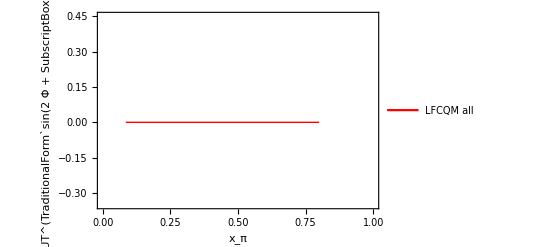

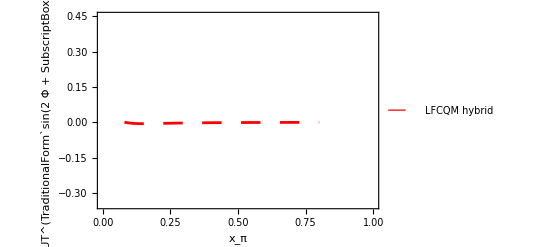

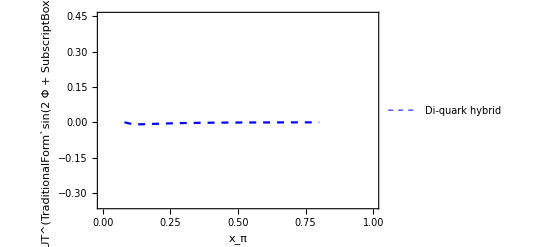

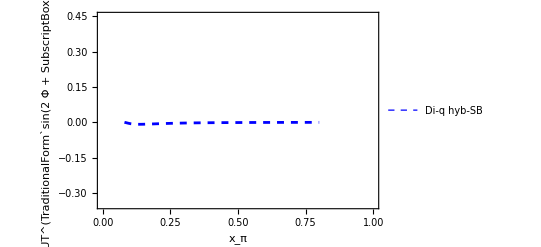

```mathematica
plotBarbAUTsin2ϕpϕbxa=Plot[BarbAUTsin2ϕpϕbqint[xa,28/(xa stot),28],{xa,0.085,0.8},PlotRange->{{0,1},{-.35,.45}},Frame->True,FrameLabel->{"x_π","A_UT^(TraditionalForm`sin(2  Φ + SubscriptBox[Φ, b]))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Red,Thick}},PlotLegends->Placed[{Style["LFCQM all",9.5]},{.25,.3}]]


plotLFChybridAUTsin2ϕpϕbxa=Plot[LFChybridAUTsin2ϕpϕbqint[xa,28/(xa stot),28],{xa,0.0801,0.8},PlotRange->{{0,1},{-.35,.45}},Frame->True,FrameLabel->{"x_π","A_UT^(TraditionalForm`sin(2  Φ + SubscriptBox[Φ, b]))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Red,Dashing[Large],Thickness[0.005]}},PlotLegends->Placed[{Style["LFCQM hybrid",9.5]},{.25,.2}]]


plotDQhybridAUTsin2ϕpϕbxa=Plot[DQhybridAUTsin2ϕpϕbqint[xa,28/(xa stot),28],{xa,0.0801,0.8},PlotRange->{{0,1},{-.35,.45}},Frame->True,FrameLabel->{"x_π","A_UT^(TraditionalForm`sin(2  Φ + SubscriptBox[Φ, b]))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Blue,Dashed,Thickness[0.004]}},PlotLegends->Placed[{Style["Di-quark hybrid",9.5]},{.25,.1}]]
(* Legend adjustment : *)
plotDQhybridAUTsin2ϕpϕbxa2=Plot[DQhybridAUTsin2ϕpϕbqint[xa,28/(xa stot),28],{xa,0.0801,0.8},PlotRange->{{0,1},{-.35,.45}},Frame->True,FrameLabel->{"x_π","A_UT^(TraditionalForm`sin(2  Φ + SubscriptBox[Φ, b]))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Blue,Dashed,Thickness[0.005]}},PlotLegends->Placed[{Style["Di-q hyb-SB",9.5]},{.25,.25}]]
```

x_p-dependent

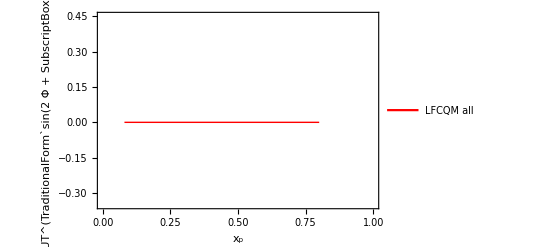

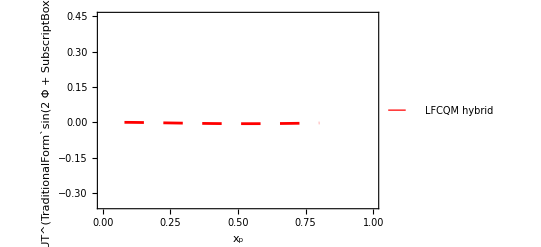

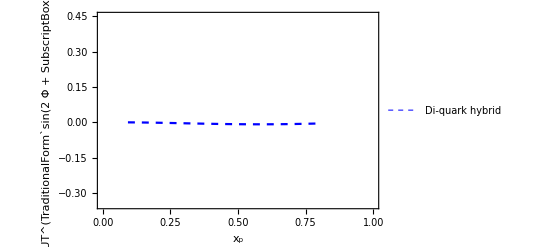

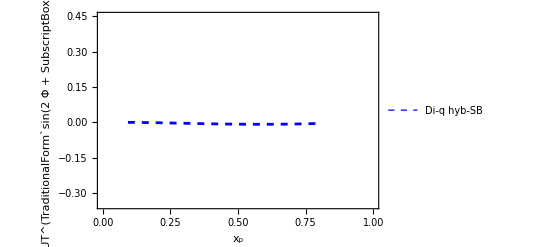

```mathematica
plotBarbAUTsin2ϕpϕbxb=Plot[BarbAUTsin2ϕpϕbqint[28/(xb stot),xb,28],{xb,0.0801,0.8},PlotRange->{{0,1},{-.35,.45}},Frame->True,FrameLabel->{"x_p","A_UT^(TraditionalForm`sin(2  Φ + SubscriptBox[Φ, b]))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Red,Thick}},PlotLegends->Placed[{Style["LFCQM all",9.5]},{.75,.9}]]

plotLFChybridAUTsin2ϕpϕbxb=Plot[LFChybridAUTsin2ϕpϕbqint[28/(xb stot),xb,28],{xb,0.0801,0.8},PlotRange->{{0,1},{-.35,.45}},Frame->True,FrameLabel->{"x_p","A_UT^(TraditionalForm`sin(2  Φ + SubscriptBox[Φ, b]))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Red,Dashing[Large],Thickness[0.005]}},PlotLegends->Placed[{Style["LFCQM hybrid",9.5]},{.75,.8}]]


plotDQhybridAUTsin2ϕpϕbxb=Plot[DQhybridAUTsin2ϕpϕbqint[28/(xb stot),xb,28],{xb,0.093,0.8},PlotRange->{{0,1},{-.35,.45}},Frame->True,FrameLabel->{"x_p","A_UT^(TraditionalForm`sin(2  Φ + SubscriptBox[Φ, b]))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Blue,Dashed,Thickness[0.004]}},PlotLegends->Placed[{Style["Di-quark hybrid",9.5]},{.75,.7}]]
(* Legend adjustment : *)
plotDQhybridAUTsin2ϕpϕbxb2=Plot[DQhybridAUTsin2ϕpϕbqint[28/(xb stot),xb,28],{xb,0.093,0.8},PlotRange->{{0,1},{-.35,.45}},Frame->True,FrameLabel->{"x_p","A_UT^(TraditionalForm`sin(2  Φ + SubscriptBox[Φ, b]))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Blue,Dashed,Thickness[0.005]}},PlotLegends->Placed[{Style["Di-q hyb-SB",9.5]},{.75,.85}]]
```

q_T-dependent

```mathematica
(*** qT dependence with integration over xa ***)
shortDQhybridAUTsin2ϕpϕbqTa=Interpolation[DisDQhybridAUTsin2ϕpϕbqTa[28,.2]];
shortLFChybridAUTsin2ϕpϕbqTa=Interpolation[DisLFChybridAUTsin2ϕpϕbqTa[28,.2]];
shortBarbAUTsin2ϕpϕbqTa=Interpolation[DisBarbAUTsin2ϕpϕbqTa[28,.2]];


(*** qT dependence with integration over xa ***)
shortDQhybridAUTsin2ϕpϕbqTb=Interpolation[DisDQhybridAUTsin2ϕpϕbqTb[28,.2]];
shortLFChybridAUTsin2ϕpϕbqTb=Interpolation[DisLFChybridAUTsin2ϕpϕbqTb[28,.2]];
shortBarbAUTsin2ϕpϕbqTb=Interpolation[DisBarbAUTsin2ϕpϕbqTb[28,.2]];
```

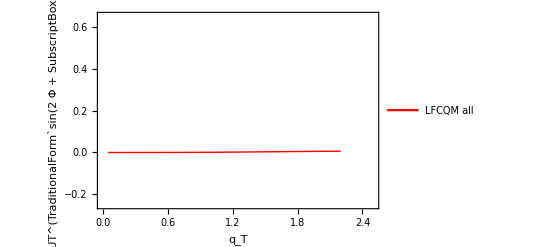

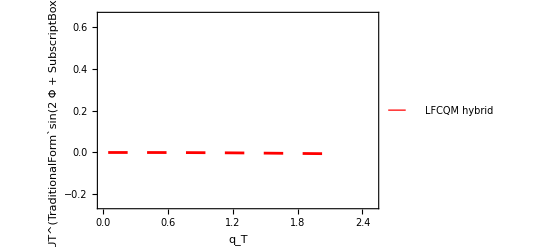

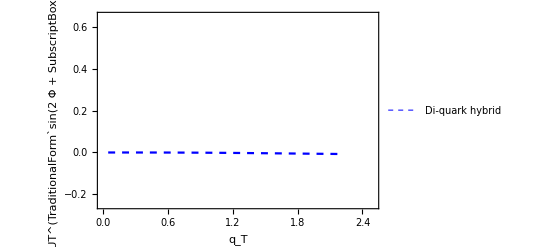

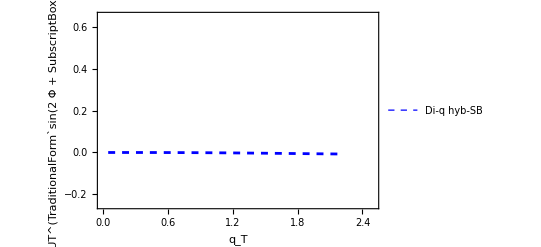

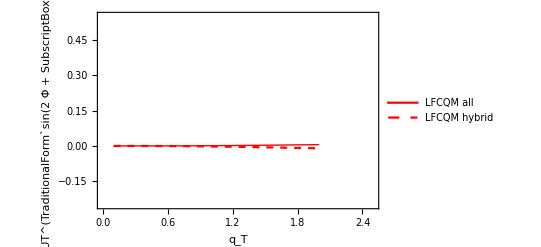

```mathematica
plotBarbAUTsin2ϕpϕbqTa=Plot[shortBarbAUTsin2ϕpϕbqTa[qT],{qT,0.05,2.2},PlotRange->{{0,2.5},{-.25,.65}},Frame->True,FrameLabel->{"q_T","A_UT^(TraditionalForm`sin(2  Φ + SubscriptBox[Φ, b]))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Red,Thick}},PlotLegends->Placed[{Style["LFCQM all",9.5]},{.75,.9}]]


plotLFChybridAUTsin2ϕpϕbqTa=Plot[shortLFChybridAUTsin2ϕpϕbqTa[qT],{qT,0.05,2.2},PlotRange->{{0,2.5},{-.25,.65}},Frame->True,FrameLabel->{"q_T","A_UT^(TraditionalForm`sin(2  Φ + SubscriptBox[Φ, b]))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Red,Dashing[Large],Thickness[0.005]}},PlotLegends->Placed[{Style["LFCQM hybrid",9.5]},{.75,.8}]]

plotDQhybridAUTsin2ϕpϕbqTa=Plot[shortDQhybridAUTsin2ϕpϕbqTa[qT],{qT,0.05,2.2},PlotRange->{{0,2.5},{-.25,.65}},Frame->True,FrameLabel->{"q_T","A_UT^(TraditionalForm`sin(2  Φ + SubscriptBox[Φ, b]))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Blue,Dashed,Thickness[0.004]}},PlotLegends->Placed[{Style["Di-quark hybrid",9.5]},{.75,.7}]]
(* Legend adjustment : *)
plotDQhybridAUTsin2ϕpϕbqTa2=Plot[shortDQhybridAUTsin2ϕpϕbqTa[qT],{qT,0.05,2.2},PlotRange->{{0,2.5},{-.25,.65}},Frame->True,FrameLabel->{"q_T","A_UT^(TraditionalForm`sin(2  Φ + SubscriptBox[Φ, b]))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Blue,Dashed,Thickness[0.005]}},PlotLegends->Placed[{Style["Di-q hyb-SB",9.5]},{.75,.85}]]


plotAUTsin2ϕpϕbqTb=Plot[{shortBarbAUTsin2ϕpϕbqTb[qT],shortLFChybridAUTsin2ϕpϕbqTb[qT]},{qT,0.1,2.0},PlotRange->{{0,2.5},{-.25,.55}},Frame->True,FrameLabel->{"q_T","A_UT^(TraditionalForm`sin(2  Φ + SubscriptBox[Φ, b]))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Red,Thick},{Red,Dashed}},PlotLegends->Placed[{Style["LFCQM all",9.5],Style["LFCQM hybrid",9.5]},{.75,.8}]]
```

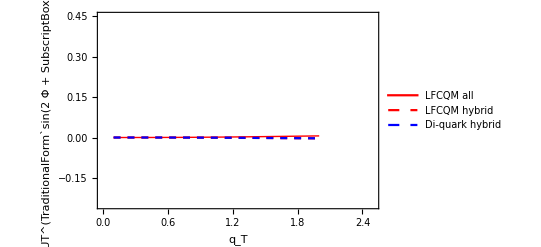

```mathematica
plotAUTsin2ϕpϕbqTnaive=Plot[{BarbAUTsin2ϕpϕb[0.5,0.17,28,qT],LFChybridAUTsin2ϕpϕb[0.5,0.17,28,qT],DQhybridAUTsin2ϕpϕb[0.5,0.17,28,qT]},{qT,0.1,2.0},PlotRange->{{0,2.5},{-.25,.45}},Frame->True,FrameLabel->{"q_T","A_UT^(TraditionalForm`sin(2  Φ + SubscriptBox[Φ, b]))"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Red,Thick},{Red,Dashed},{Blue,Dashed}},PlotLegends->Placed[{Style["LFCQM all",9.5],Style["LFCQM hybrid",9.5],Style["Di-quark hybrid",9.5]},{.75,.8}]]
```

#### Experimental Plots

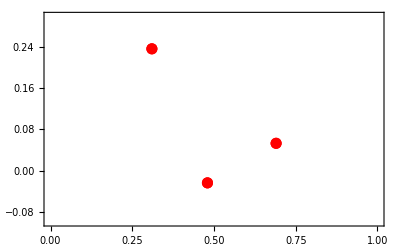

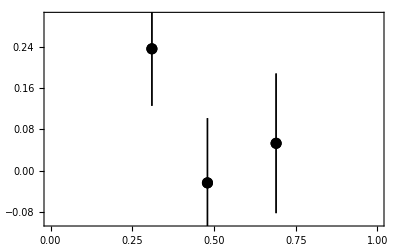

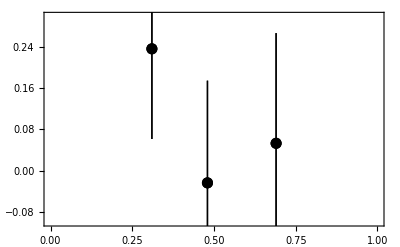

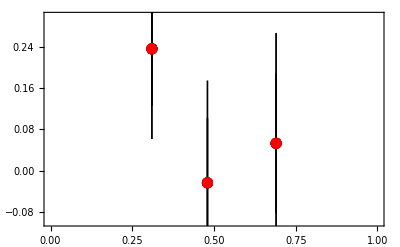

```mathematica
Clear[data,tab];
data=Cases[Import["./data/A_T_sin_2phiCS_p_phiS_x_pi.dat","Table"],{_?NumberQ,___}]; 
tabpoints =  Table[{{data[[i]][[4]],data[[i]][[8]]}},{i,Length[data]}];
tab =  Table[{{data[[i]][[4]],data[[i]][[8]]},ErrorBar[data[[i]][[9]]]},{i,Length[data]},{j,1}];
tabsys =  Table[{{data[[i]][[4]],data[[i]][[8]]},ErrorBar[Sqrt[data[[i]][[9]]^2+data[[i]][[10]]^2]]},{i,Length[data]},{j,1}];
plotdataCOMPASSpimPoints=ListPlot[tabpoints, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpimsys=ErrorListPlot[tabsys, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdata3xa = Show[plotdataCOMPASSpim, plotdataCOMPASSpimsys,plotdataCOMPASSpimPoints]
```

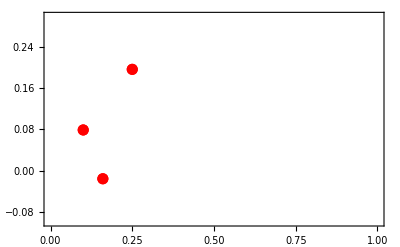

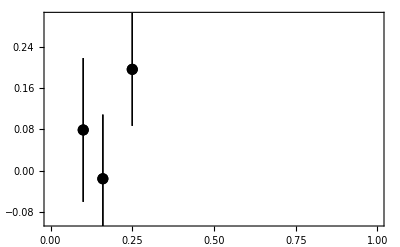

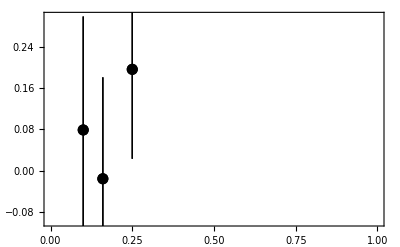

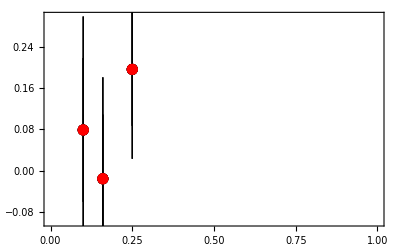

```mathematica
Clear[data,tab];
data=Cases[Import["./data/A_T_sin_2phiCS_p_phiS_x_N.dat","Table"],{_?NumberQ,___}]; 
tabpoints =  Table[{{data[[i]][[3]],data[[i]][[8]]}},{i,Length[data]}];
tab =  Table[{{data[[i]][[3]],data[[i]][[8]]},ErrorBar[data[[i]][[9]]]},{i,Length[data]},{j,1}];
tabsys =  Table[{{data[[i]][[3]],data[[i]][[8]]},ErrorBar[Sqrt[data[[i]][[9]]^2+data[[i]][[10]]^2]]},{i,Length[data]},{j,1}];
plotdataCOMPASSpimPoints=ListPlot[tabpoints, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpimsys=ErrorListPlot[tabsys, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdata3xb = Show[plotdataCOMPASSpim, plotdataCOMPASSpimsys,plotdataCOMPASSpimPoints]
```

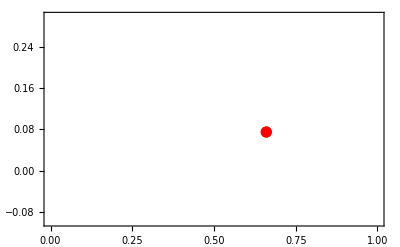

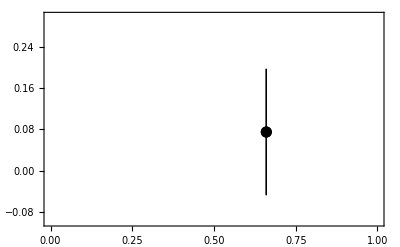

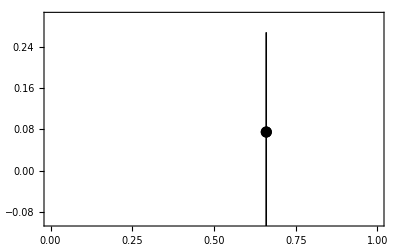

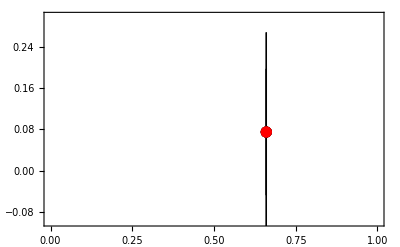

```mathematica
Clear[data,tab];
data=Cases[Import["./data/A_T_sin_2phiCS_p_phiS_q_T.dat","Table"],{_?NumberQ,___}]; 
tabpoints =  Table[{{data[[i]][[6]],data[[i]][[8]]}},{i,Length[data]}];
tab =  Table[{{data[[i]][[6]],data[[i]][[8]]},ErrorBar[data[[i]][[9]]]},{i,Length[data]},{j,1}];
tabsys =  Table[{{data[[i]][[6]],data[[i]][[8]]},ErrorBar[Sqrt[data[[i]][[9]]^2+data[[i]][[10]]^2]]},{i,Length[data]},{j,1}];
plotdataCOMPASSpimPoints=ListPlot[tabpoints, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdataCOMPASSpimsys=ErrorListPlot[tabsys, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Black,Thin,PointSize[0.02],Opacity[1.]}}] 
plotdata3qT = Show[plotdataCOMPASSpim, plotdataCOMPASSpimsys,plotdataCOMPASSpimPoints]
```

#### Final Plots

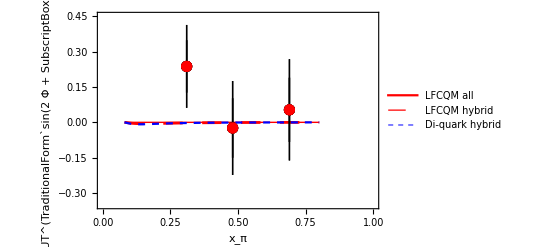

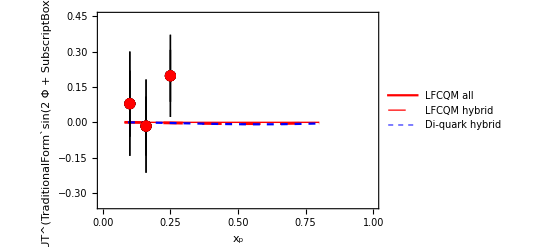

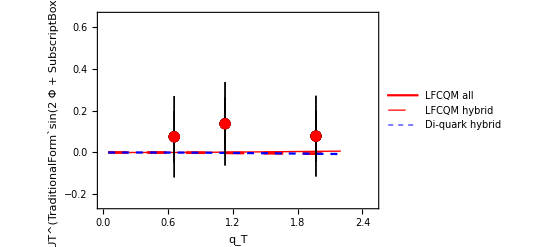

```mathematica
Show[plotBarbAUTsin2ϕpϕbxa,plotLFChybridAUTsin2ϕpϕbxa,plotDQhybridAUTsin2ϕpϕbxa,plotdata3xa]
Show[plotBarbAUTsin2ϕpϕbxb,plotLFChybridAUTsin2ϕpϕbxb,plotDQhybridAUTsin2ϕpϕbxb,plotdata3xb]
Show[plotBarbAUTsin2ϕpϕbqTa,plotLFChybridAUTsin2ϕpϕbqTa,plotDQhybridAUTsin2ϕpϕbqTa,plotdata3qT]
```

### A_UU^(cos 2Φ)

#### Numerical Calculations

Di-quark hybrid

```mathematica
(** BM from Di-quark and the rest from parametrizations **)
DQhybridAUUcos2ϕ[xa_,xb_,Q2_,qT_]:=DQhybridFUUcos2ϕ[xa,xb,Q2,qT]/FUU1[xa,xb,Q2,qT]


DQhybridAUUcos2ϕqint[xa_,xb_,Q2_]:=DQhybridFUUcos2ϕqint[xa,xb,Q2]/FUU1qint[xa,xb,Q2]


DQhybridAUUcos2ϕqTa[Q2_,qT_]:=DQhybridFUUcos2ϕqTa[Q2,qT]/FUU1qTa[Q2,qT]
DisDQhybridAUUcos2ϕqTa[Q2_,step_]:=Table[{qT,DQhybridAUUcos2ϕqTa[Q2,qT]},{qT,.02,2.2,step}]

DQhybridAUUcos2ϕqTb[Q2_,qT_]:=DQhybridFUUcos2ϕqTb[Q2,qT]/FUU1qTb[Q2,qT]
DisDQhybridAUUcos2ϕqTb[Q2_,step_]:=Table[{qT,DQhybridAUUcos2ϕqTb[Q2,qT]},{qT,.02,2.2,step}]



DQhybridFUUcos2ϕ[xa_,xb_,Q2_,qT_]:=(4Ma  Mb)/(π qw["BM","BM"]^3)qT^2 ⅇ^(-qT^2/qw["BM","BM"])   ∑_(q=1)^3 Subscript[e, q]^2(OverBar[Subscript[DQh1p1a, q]][xa,Q2] Subscript[h1p1b, q][xb,Q2]+OverBar[Subscript[h1p1b, q]][xb,Q2] Subscript[DQh1p1a, q][xa,Q2])

DQhybridFUUcos2ϕqint[xa_,xb_,Q2_]:=(4 Ma  Mb)/qw["BM","BM"]  ∑_(q=1)^3 Subscript[e, q]^2(OverBar[Subscript[DQh1p1a, q]][xa,Q2] Subscript[h1p1b, q][xb,Q2]+OverBar[Subscript[h1p1b, q]][xb,Q2] Subscript[DQh1p1a, q][xa,Q2])


DQhybridFUUcos2ϕqTa[Q2_,qT_]:=NIntegrate[DQhybridFUUcos2ϕ[xa,Q2/(xa stot),Q2,qT],{xa,Q2/stot,.9}]
DQhybridFUUcos2ϕqTb[Q2_,qT_]:=NIntegrate[DQhybridFUUcos2ϕ[Q2/(xb stot),xb,Q2,qT],{xb,Q2/stot,.9}]



Subscript[h1p1b, 1][xb_,Q2_]:=h1p1u[xb,Q2];Subscript[h1p1b, 2][xb_,Q2_]:=h1p1d[xb,Q2];Subscript[h1p1b, 3][xb_,Q2_]:=0;OverBar[Subscript[h1p1b, 1]][xb_,Q2_]:=0;OverBar[Subscript[h1p1b, 2]][xb_,Q2_]:=0;OverBar[Subscript[h1p1b, 3]][xb_,Q2_]:=0;
```

LFCQM hybrid

```mathematica
(** BM from Barbara and the rest from parametrization **)
LFChybridAUUcos2ϕ[xa_,xb_,Q2_,qT_]:=LFChybridFUUcos2ϕ[xa,xb,Q2,qT]/FUU1[xa,xb,Q2,qT]


LFChybridAUUcos2ϕqint[xa_,xb_,Q2_]:=LFChybridFUUcos2ϕqint[xa,xb,Q2]/FUU1qint[xa,xb,Q2]


LFChybridAUUcos2ϕqTa[Q2_,qT_]:=LFChybridFUUcos2ϕqTa[Q2,qT]/FUU1qTa[Q2,qT]
DisLFChybridAUUcos2ϕqTa[Q2_,step_]:=Table[{qT,LFChybridAUUcos2ϕqTa[Q2,qT]},{qT,.02,2.2,step}]

LFChybridAUUcos2ϕqTb[Q2_,qT_]:=LFChybridFUUcos2ϕqTb[Q2,qT]/FUU1qTb[Q2,qT]
DisLFChybridAUUcos2ϕqTb[Q2_,step_]:=Table[{qT,LFChybridAUUcos2ϕqTb[Q2,qT]},{qT,.02,2.2,step}]



LFChybridFUUcos2ϕ[xa_,xb_,Q2_,qT_]:=(4Ma  Mb)/(π qw["BM","BM"]^3)qT^2 ⅇ^(-qT^2/qw["BM","BM"])   ∑_(q=1)^3 Subscript[e, q]^2(OverBar[Subscript[Bh1p1a, q]][xa,Q2] Subscript[h1p1b, q][xb,Q2]+OverBar[Subscript[h1p1b, q]][xb,Q2] Subscript[Bh1p1a, q][xa,Q2])

LFChybridFUUcos2ϕqint[xa_,xb_,Q2_]:=(4 Ma  Mb)/qw["BM","BM"]  ∑_(q=1)^3 Subscript[e, q]^2(OverBar[Subscript[Bh1p1a, q]][xa,Q2] Subscript[h1p1b, q][xb,Q2]+OverBar[Subscript[h1p1b, q]][xb,Q2] Subscript[Bh1p1a, q][xa,Q2])


LFChybridFUUcos2ϕqTa[Q2_,qT_]:=NIntegrate[LFChybridFUUcos2ϕ[xa,Q2/(xa stot),Q2,qT],{xa,Q2/stot,.9}]
LFChybridFUUcos2ϕqTb[Q2_,qT_]:=NIntegrate[LFChybridFUUcos2ϕ[Q2/(xb stot),xb,Q2,qT],{xb,Q2/stot,.9}]
```

LFCQM all

```mathematica
(*** All inputs from Barbara's model **)
 
BarbAUUcos2ϕ[xa_,xb_,Q2_,qT_]:=BarbFUUcos2ϕ[xa,xb,Q2,qT]/BarbFUU1[xa,xb,Q2,qT]


BarbAUUcos2ϕqint[xa_,xb_,Q2_]:=BarbFUUcos2ϕqint[xa,xb,Q2]/BarbFUU1qint[xa,xb,Q2]


BarbAUUcos2ϕqTa[Q2_,qT_]:=BarbFUUcos2ϕqTa[Q2,qT]/BarbFUU1qTa[Q2,qT]
DisBarbAUUcos2ϕqTa[Q2_,step_]:=Table[{qT,BarbAUUcos2ϕqTa[Q2,qT]},{qT,.02,2.2,step}]

BarbAUUcos2ϕqTb[Q2_,qT_]:=BarbFUUcos2ϕqTb[Q2,qT]/BarbFUU1qTb[Q2,qT]
DisBarbAUUcos2ϕqTb[Q2_,step_]:=Table[{qT,BarbAUUcos2ϕqTb[Q2,qT]},{qT,.02,2.2,step}]




BarbFUUcos2ϕ[xa_,xb_,Q2_,qT_]:=(4 Ma  Mb)/(π qw["BM","BM"]^3)qT^2 ⅇ^(-qT^2/qw["BM","BM"])   ∑_(q=1)^3 Subscript[e, q]^2(OverBar[Subscript[Bh1p1a, q]][xa,Q2] Subscript[Bh1p1b, q][xb,Q2]+OverBar[Subscript[Bh1p1b, q]][xb,Q2] Subscript[Bh1p1a, q][xa,Q2])

BarbFUUcos2ϕqint[xa_,xb_,Q2_]:=(4 Ma  Mb)/qw["BM","BM"]   ∑_(q=1)^3 Subscript[e, q]^2(OverBar[Subscript[Bh1p1a, q]][xa,Q2] Subscript[Bh1p1b, q][xb,Q2]+OverBar[Subscript[Bh1p1b, q]][xb,Q2] Subscript[Bh1p1a, q][xa,Q2])


BarbFUUcos2ϕqTa[Q2_,qT_]:=NIntegrate[BarbFUUcos2ϕ[xa,Q2/(xa stot),Q2,qT],{xa,Q2/stot,.9}]
BarbFUUcos2ϕqTb[Q2_,qT_]:=NIntegrate[BarbFUUcos2ϕ[Q2/(xb stot),xb,Q2,qT],{xb,Q2/stot,.9}]



Subscript[Bh1p1b, 1][x_,Q2_]:=Barbxh1perp1u[x]/x;Subscript[Bh1p1b, 2][x_,Q2_]:=Barbxh1perp1d[x]/x;Subscript[Bh1p1b, 3][x_,Q2_]:=0;OverBar[Subscript[Bh1p1b, 1]][x_,Q2_]:=0 ;OverBar[Subscript[Bh1p1b, 2]][xa_,Q2_]:=0 ;OverBar[Subscript[Bh1p1b, 3]][xa_,Q2_]:=0
```

#### Theoretical Plots

x_π-dependent

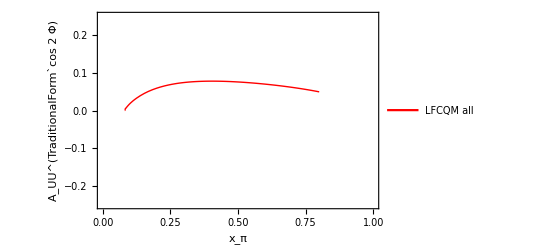

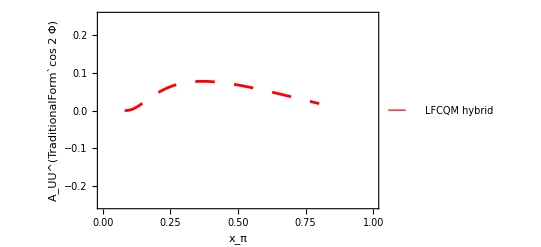

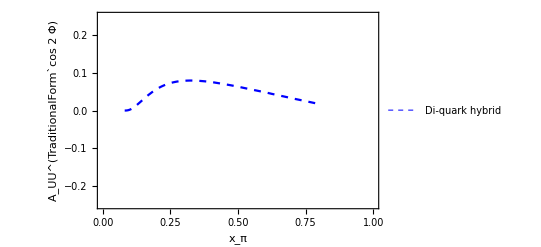

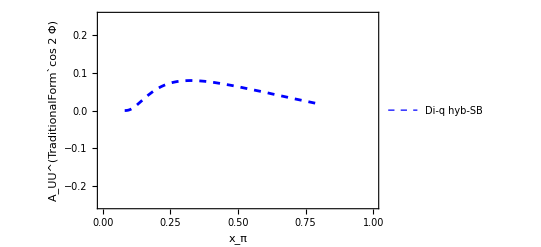

```mathematica
plotBarbAUUcos2ϕxa=Plot[BarbAUUcos2ϕqint[xa,28/(xa stot),28],{xa,0.081,0.8},PlotRange->{{0,1},{-.25,.25}},Frame->True,FrameLabel->{"x_π","A_UU^(TraditionalForm`cos 2  Φ)"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Red,Thick}},PlotLegends->Placed[{Style["LFCQM all",9.5]},{.75,.3}]]

plotLFChybridAUUcos2ϕxa=Plot[LFChybridAUUcos2ϕqint[xa,28/(xa stot),28],{xa,0.081,0.8},PlotRange->{{0,1},{-.25,.25}},Frame->True,FrameLabel->{"x_π","A_UU^(TraditionalForm`cos 2  Φ)"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Red,Dashing[Large],Thickness[0.005]}},PlotLegends->Placed[{Style["LFCQM hybrid",9.5]},{.75,.2}]]

plotDQhybridAUUcos2ϕxa=Plot[DQhybridAUUcos2ϕqint[xa,28/(xa stot),28],{xa,0.081,0.8},PlotRange->{{0,1},{-.25,.25}},Frame->True,FrameLabel->{"x_π","A_UU^(TraditionalForm`cos 2  Φ)"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Blue,Dashed,Thickness[0.004]}},PlotLegends->Placed[{Style["Di-quark hybrid",9.5]},{.75,.1}]]
(* Legend adjustment : *)
plotDQhybridAUUcos2ϕxa2=Plot[DQhybridAUUcos2ϕqint[xa,28/(xa stot),28],{xa,0.081,0.8},PlotRange->{{0,1},{-.25,.25}},Frame->True,FrameLabel->{"x_π","A_UU^(TraditionalForm`cos 2  Φ)"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Blue,Dashed,Thickness[0.005]}},PlotLegends->Placed[{Style["Di-q hyb-SB",9.5]},{.75,.25}]]
```

x_p-dependent

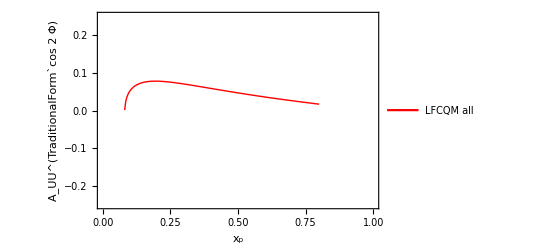

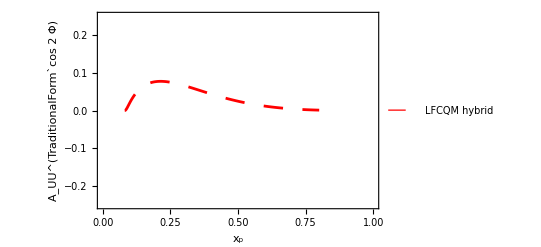

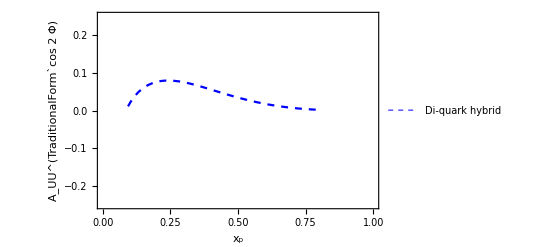

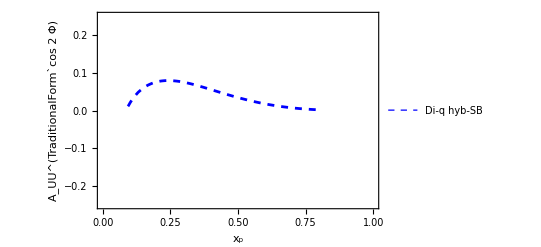

```mathematica
plotBarbAUUcos2ϕxb=Plot[BarbAUUcos2ϕqint[28/(xb stot),xb,28],{xb,0.081,0.8},PlotRange->{{0,1},{-.25,.25}},Frame->True,FrameLabel->{"x_p","A_UU^(TraditionalForm`cos 2  Φ)"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Red,Thick}},PlotLegends->Placed[{Style["LFCQM all",9.5]},{.75,.3}]]


plotLFChybridAUUcos2ϕxb=Plot[LFChybridAUUcos2ϕqint[28/(xb stot),xb,28],{xb,0.081,0.8},PlotRange->{{0,1},{-.25,.25}},Frame->True,FrameLabel->{"x_p","A_UU^(TraditionalForm`cos 2  Φ)"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Red,Dashing[Large],Thickness[0.005]}},PlotLegends->Placed[{Style["LFCQM hybrid",9.5]},{.75,.2}]]

plotDQhybridAUUcos2ϕxb=Plot[DQhybridAUUcos2ϕqint[28/(xb stot),xb,28],{xb,0.093,0.8},PlotRange->{{0,1},{-.25,.25}},Frame->True,FrameLabel->{"x_p","A_UU^(TraditionalForm`cos 2  Φ)"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Blue,Dashed,Thickness[0.004]}},PlotLegends->Placed[{Style["Di-quark hybrid",9.5]},{.75,.1}]]
(* Legent adjustment : *)
plotDQhybridAUUcos2ϕxb2=Plot[DQhybridAUUcos2ϕqint[28/(xb stot),xb,28],{xb,0.093,0.8},PlotRange->{{0,1},{-.25,.25}},Frame->True,FrameLabel->{"x_p","A_UU^(TraditionalForm`cos 2  Φ)"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Blue,Dashed,Thickness[0.005]}},PlotLegends->Placed[{Style["Di-q hyb-SB",9.5]},{.75,.25}]]
```

q_T-dependent

```mathematica
(*** qT dependence with integration over xa ***)
shortDQhybridAUUcos2ϕqTa=Interpolation[DisDQhybridAUUcos2ϕqTa[28,.2]];
shortLFChybridAUUcos2ϕqTa=Interpolation[DisLFChybridAUUcos2ϕqTa[28,.2]];
shortBarbAUUcos2ϕqTa=Interpolation[DisBarbAUUcos2ϕqTa[28,.2]];

(*** qT dependence with integration over xb ***)
shortDQhybridAUUcos2ϕqTb=Interpolation[DisDQhybridAUUcos2ϕqTb[28,.2]];
shortLFChybridAUUcos2ϕqTb=Interpolation[DisLFChybridAUUcos2ϕqTb[28,.2]];
shortBarbAUUcos2ϕqTb=Interpolation[DisBarbAUUcos2ϕqTb[28,.2]];
```

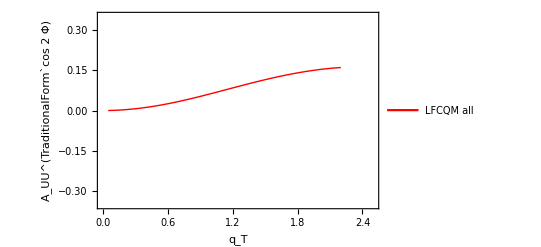

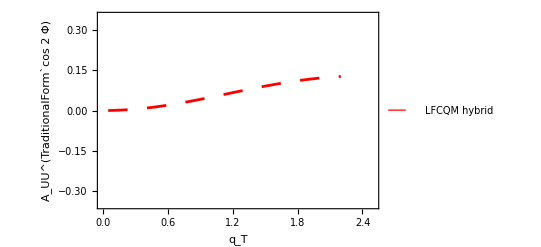

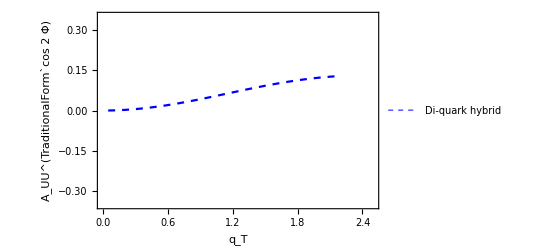

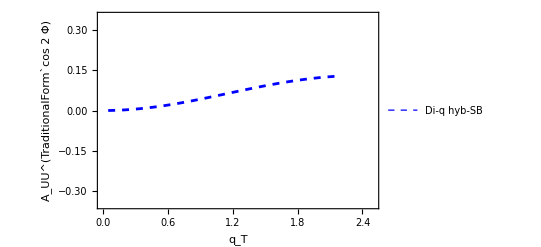

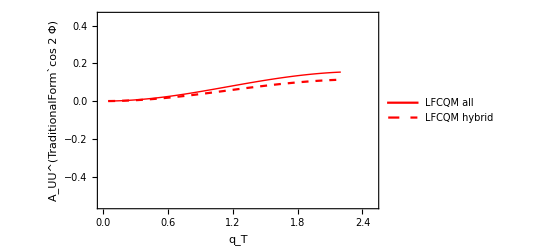

```mathematica
plotBarbAUUcos2ϕqTa=Plot[shortBarbAUUcos2ϕqTa[qT],{qT,0.05,2.2},PlotRange->{{0,2.5},{-.35,.35}},Frame->True,FrameLabel->{"q_T","A_UU^(TraditionalForm`cos 2  Φ)"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Red,Thick}},PlotLegends->Placed[{Style["LFCQM all",9.5]},{.75,.3}]]


plotLFChybridAUUcos2ϕqTa=Plot[shortLFChybridAUUcos2ϕqTa[qT],{qT,0.05,2.2},PlotRange->{{0,2.5},{-.35,.35}},Frame->True,FrameLabel->{"q_T","A_UU^(TraditionalForm`cos 2  Φ)"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Red,Dashing[Large],Thickness[0.005]}},PlotLegends->Placed[{Style["LFCQM hybrid",10]},{.75,.2}]]

plotDQhybridAUUcos2ϕqTa=Plot[shortDQhybridAUUcos2ϕqTa[qT],{qT,0.05,2.2},PlotRange->{{0,2.5},{-.35,.35}},Frame->True,FrameLabel->{"q_T","A_UU^(TraditionalForm`cos 2  Φ)"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Blue,Dashed,Thickness[0.004]}},PlotLegends->Placed[{Style["Di-quark hybrid",10]},{.75,.1}]]
(* Legend adjustment : *)
plotDQhybridAUUcos2ϕqTa2=Plot[shortDQhybridAUUcos2ϕqTa[qT],{qT,0.05,2.2},PlotRange->{{0,2.5},{-.35,.35}},Frame->True,FrameLabel->{"q_T","A_UU^(TraditionalForm`cos 2  Φ)"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Blue,Dashed,Thickness[0.005]}},PlotLegends->Placed[{Style["Di-q hyb-SB",10]},{.75,.25}]]


plotAUUcos2ϕqTb=Plot[{shortBarbAUUcos2ϕqTb[qT],shortLFChybridAUUcos2ϕqTb[qT]},{qT,0.05,2.2},PlotRange->{{0,2.5},{-.55,.45}},Frame->True,FrameLabel->{"q_T","A_UU^(TraditionalForm`cos 2  Φ)"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Red,Thick},{Red,Dashed}},PlotLegends->Placed[{Style["LFCQM all",9.5],Style["LFCQM hybrid",9.5]},{.75,.2}]]
```

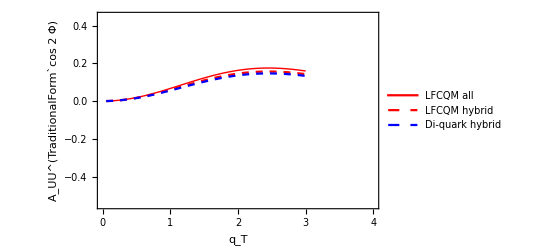

```mathematica
plotAUUcos2ϕqTnaive=Plot[{BarbAUUcos2ϕ[0.5,0.17,28,qT],LFChybridAUUcos2ϕ[0.5,0.17,28,qT],DQhybridAUUcos2ϕ[0.5,0.17,28,qT]},{qT,0.05,3},PlotRange->{{0,4},{-.55,.45}},Frame->True,FrameLabel->{"q_T","A_UU^(TraditionalForm`cos 2  Φ)"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Red,Thick},{Red,Dashed},{Blue,Dashed}},PlotLegends->Placed[{Style["LFCQM all",9.5],Style["LFCQM hybrid",9.5],Style["Di-quark hybrid",9.5]},{.75,.2}]]
```

#### Final Plots

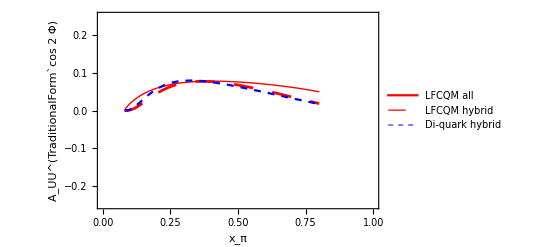

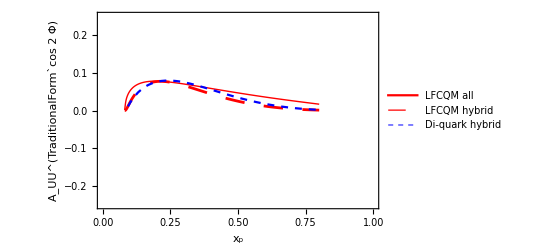

-Graphics-

-Graphics-

```mathematica
Show[plotBarbAUUcos2ϕxa,plotLFChybridAUUcos2ϕxa,plotDQhybridAUUcos2ϕxa]
Show[plotBarbAUUcos2ϕxb,plotLFChybridAUUcos2ϕxb,plotDQhybridAUUcos2ϕxb]
Show[plotBarbAUUcos2ϕqTa,plotLFChybridAUUcos2ϕqTa,plotDQhybridAUUcos2ϕqTa]
Show[plotAUUcos2ϕqTb]
```

### A_UL^(sin 2Φ)

#### Numerical Calculations

Di-quark hybrid

```mathematica
DQhybridAULsin2ϕ[xa_,xb_,Q2_,qT_]:=DQhybridFULsin2ϕ[xa,xb,Q2,qT]/FUU1[xa,xb,Q2,qT]


DQhybridAULsin2ϕqint[xa_,xb_,Q2_]:=DQhybridFULsin2ϕqint[xa,xb,Q2]/FUU1qint[xa,xb,Q2]


DQhybridAULsin2ϕqTa[Q2_,qT_]:=DQhybridFULsin2ϕqTa[Q2,qT]/FUU1qTa[Q2,qT]
DisDQhybridAULsin2ϕqTa[Q2_,step_]:=Table[{qT,DQhybridAULsin2ϕqTa[Q2,qT]},{qT,.02,2.2,step}]


DQhybridAULsin2ϕqTb[Q2_,qT_]:=DQhybridFULsin2ϕqTb[Q2,qT]/FUU1qTb[Q2,qT]
DisDQhybridAULsin2ϕqTb[Q2_,step_]:=Table[{qT,DQhybridAULsin2ϕqTb[Q2,qT]},{qT,.02,2.2,step}]



DQhybridFULsin2ϕ[xa_,xb_,Q2_,qT_]:=-(4Ma  Mb)/(π qw["BM","WG"]^3)qT^2 ⅇ^(-qT^2/qw["BM","WG"]) ∑_(q=1)^3 Subscript[e, q]^2(OverBar[Subscript[DQh1p1a, q]][xa,Q2] Subscript[h1Lp1b, q][xb,Q2]+OverBar[Subscript[h1Lp1b, q]][xb,Q2] Subscript[DQh1p1a, q][xa,Q2])

DQhybridFULsin2ϕqint[xa_,xb_,Q2_]:=-(4 Ma  Mb)/qw["BM","WG"]   ∑_(q=1)^3 Subscript[e, q]^2(OverBar[Subscript[DQh1p1a, q]][xa,Q2] Subscript[h1Lp1b, q][xb,Q2]+OverBar[Subscript[h1Lp1b, q]][xb,Q2] Subscript[DQh1p1a, q][xa,Q2])



DQhybridFULsin2ϕqTa[Q2_,qT_]:=NIntegrate[DQhybridFULsin2ϕ[xa,Q2/(xa stot),Q2,qT],{xa,Q2/stot,.9}]
DQhybridFULsin2ϕqTb[Q2_,qT_]:=NIntegrate[DQhybridFULsin2ϕ[Q2/(xb stot),xb,Q2,qT],{xb,Q2/stot,.9}]



Subscript[h1Lp1b, 1][xb_,Q2_]:=h1Lp1u[xb];Subscript[h1Lp1b, 2][xb_,Q2_]:=h1Lp1d[xb];Subscript[h1Lp1b, 3][xb_,Q2_]:=0;OverBar[Subscript[h1Lp1b, 1]][xb_,Q2_]:=0;OverBar[Subscript[h1Lp1b, 2]][xb_,Q2_]:=0;OverBar[Subscript[h1Lp1b, 3]][xb_,Q2_]:=0;
```

LFCQM hybrid

```mathematica
LFChybridAULsin2ϕ[xa_,xb_,Q2_,qT_]:=LFChybridFULsin2ϕ[xa,xb,Q2,qT]/FUU1[xa,xb,Q2,qT]


LFChybridAULsin2ϕqint[xa_,xb_,Q2_]:=LFChybridFULsin2ϕqint[xa,xb,Q2]/FUU1qint[xa,xb,Q2]


LFChybridAULsin2ϕqTa[Q2_,qT_]:=LFChybridFULsin2ϕqTa[Q2,qT]/FUU1qTa[Q2,qT]
DisLFChybridAULsin2ϕqTa[Q2_,step_]:=Table[{qT,LFChybridAULsin2ϕqTa[Q2,qT]},{qT,.02,2.2,step}]


LFChybridAULsin2ϕqTb[Q2_,qT_]:=LFChybridFULsin2ϕqTb[Q2,qT]/FUU1qTb[Q2,qT]
DisLFChybridAULsin2ϕqTb[Q2_,step_]:=Table[{qT,LFChybridAULsin2ϕqTb[Q2,qT]},{qT,.02,2.2,step}]




LFChybridFULsin2ϕ[xa_,xb_,Q2_,qT_]:=-(4Ma  Mb)/(π qw["BM","WG"]^3)qT^2 ⅇ^(-qT^2/qw["BM","WG"]) ∑_(q=1)^3 Subscript[e, q]^2(OverBar[Subscript[Bh1p1a, q]][xa,Q2] Subscript[h1Lp1b, q][xb,Q2]+OverBar[Subscript[h1Lp1b, q]][xb,Q2] Subscript[Bh1p1a, q][xa,Q2])

LFChybridFULsin2ϕqint[xa_,xb_,Q2_]:=-(4 Ma  Mb)/qw["BM","WG"]   ∑_(q=1)^3 Subscript[e, q]^2(OverBar[Subscript[Bh1p1a, q]][xa,Q2] Subscript[h1Lp1b, q][xb,Q2]+OverBar[Subscript[h1Lp1b, q]][xb,Q2] Subscript[Bh1p1a, q][xa,Q2])



LFChybridFULsin2ϕqTa[Q2_,qT_]:=NIntegrate[LFChybridFULsin2ϕ[xa,Q2/(xa stot),Q2,qT],{xa,Q2/stot,.9}]
LFChybridFULsin2ϕqTb[Q2_,qT_]:=NIntegrate[LFChybridFULsin2ϕ[Q2/(xb stot),xb,Q2,qT],{xb,Q2/stot,.9}]
```

LFCQM all

```mathematica
(****************  Barbara's  ********************) 
BarbAULsin2ϕ[xa_,xb_,Q2_,qT_]:=BarbFULsin2ϕ[xa,xb,Q2,qT]/BarbFUU1[xa,xb,Q2,qT]


BarbAULsin2ϕqint[xa_,xb_,Q2_]:=BarbFULsin2ϕqint[xa,xb,Q2]/BarbFUU1qint[xa,xb,Q2]


BarbAULsin2ϕqTa[Q2_,qT_]:=BarbFULsin2ϕqTa[Q2,qT]/BarbFUU1qTa[Q2,qT]
DisBarbAULsin2ϕqTa[Q2_,step_]:=Table[{qT,BarbAULsin2ϕqTa[Q2,qT]},{qT,.02,2.2,step}]


BarbAULsin2ϕqTb[Q2_,qT_]:=BarbFULsin2ϕqTb[Q2,qT]/BarbFUU1qTb[Q2,qT]
DisBarbAULsin2ϕqTb[Q2_,step_]:=Table[{qT,BarbAULsin2ϕqTb[Q2,qT]},{qT,.02,2.2,step}]




BarbFULsin2ϕ[xa_,xb_,Q2_,qT_]:=-(4 Ma  Mb qT^2 ⅇ^(-qT^2/qw["BM","WG"]))/(π qw["BM","WG"]^3)   ∑_(q=1)^3 Subscript[e, q]^2(OverBar[Subscript[Bh1p1a, q]][xa,Q2] Subscript[Bh1Lp1b, q][xb,Q2]+OverBar[Subscript[Bh1Lp1b, q]][xb,Q2] Subscript[Bh1p1a, q][xa,Q2])

BarbFULsin2ϕqint[xa_,xb_,Q2_]:=-(4 Ma  Mb)/qw["BM","WG"]   ∑_(q=1)^3 Subscript[e, q]^2(OverBar[Subscript[Bh1p1a, q]][xa,Q2] Subscript[Bh1Lp1b, q][xb,Q2]+OverBar[Subscript[Bh1Lp1b, q]][xb,Q2] Subscript[Bh1p1a, q][xa,Q2])



BarbFULsin2ϕqTa[Q2_,qT_]:=NIntegrate[BarbFULsin2ϕ[xa,Q2/(xa stot),Q2,qT],{xa,Q2/stot,.9}]
BarbFULsin2ϕqTb[Q2_,qT_]:=NIntegrate[BarbFULsin2ϕ[Q2/(xb stot),xb,Q2,qT],{xb,Q2/stot,.9}]



Subscript[Bh1Lp1b, 1][x_,Q2_]:=Barbxh1Lperp1u[x]/x;Subscript[Bh1Lp1b, 2][x_,Q2_]:=Barbxh1Lperp1d[x]/x;Subscript[Bh1Lp1b, 3][x_,Q2_]:=0
OverBar[Subscript[Bh1Lp1b, 1]][x_,Q2_]:=0 ;OverBar[Subscript[Bh1Lp1b, 2]][x_,Q2_]:=0 ;OverBar[Subscript[Bh1Lp1b, 3]][x_,Q2_]:=0
```

#### Theoretical Plots

x_π-dependent

```mathematica
plotBarbAULsin2ϕxa=Plot[BarbAULsin2ϕqint[xa,28/(xa stot),25],{xa,0.081,0.8},PlotRange->{{0,1},{-.12,.12}},Frame->True,FrameLabel->{"x_π","A_UL^(TraditionalForm`sin 2  Φ)"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Red,Thick}},PlotLegends->Placed[{Style["LFCQM all",9.5]},{.75,.3}]]


plotLFChybridAULsin2ϕxa=Plot[LFChybridAULsin2ϕqint[xa,28/(xa stot),28],{xa,0.083,0.8},PlotRange->{{0,1},{-.12,.12}},Frame->True,FrameLabel->{"x_π","A_UL^(TraditionalForm`sin 2  Φ)"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Red,Dashing[Large],Thickness[0.005]}},PlotLegends->Placed[{Style["LFCQM hybrid",9.5]},{.75,.2}]]


plotDQhybridAULsin2ϕxa=Plot[DQhybridAULsin2ϕqint[xa,28/(xa stot),28],{xa,0.083,0.8},PlotRange->{{0,1},{-.12,.12}},Frame->True,FrameLabel->{"x_π","A_UL^(TraditionalForm`sin 2  Φ)"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Blue,Dashed,Thickness[0.004]}},PlotLegends->Placed[{Style["Di-quark hybrid",9.5]},{.75,.1}]]
(* Legend adjustment : *)
plotDQhybridAULsin2ϕxa2=Plot[DQhybridAULsin2ϕqint[xa,28/(xa stot),28],{xa,0.083,0.8},PlotRange->{{0,1},{-.12,.12}},Frame->True,FrameLabel->{"x_π","A_UL^(TraditionalForm`sin 2  Φ)"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Blue,Dashed,Thickness[0.005]}},PlotLegends->Placed[{Style["Di-q hyb-SB",9.5]},{.75,.25}]]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

x_p-dependent

```mathematica
plotBarbAULsin2ϕxb=Plot[BarbAULsin2ϕqint[28/(xb stot),xb,28],{xb,0.081,0.8},PlotRange->{{0,1},{-.12,.12}},Frame->True,FrameLabel->{"x_p","A_UL^(TraditionalForm`sin 2  Φ)"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Red,Thick}},PlotLegends->Placed[{Style["LFCQM all",9.5]},{.75,.3}]]


plotLFChybridAULsin2ϕxb=Plot[LFChybridAULsin2ϕqint[28/(xb stot),xb,28],{xb,0.081,0.8},PlotRange->{{0,1},{-.12,.12}},Frame->True,FrameLabel->{"x_p","A_UL^(TraditionalForm`sin 2  Φ)"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Red,Dashing[Large],Thickness[0.005]}},PlotLegends->Placed[{Style["LFCQM hybrid",9.5]},{.75,.2}]]


plotDQhybridAULsin2ϕxb=Plot[DQhybridAULsin2ϕqint[28/(xb stot),xb,28],{xb,0.093,0.8},PlotRange->{{0,1},{-.12,.12}},Frame->True,FrameLabel->{"x_p","A_UL^(TraditionalForm`sin 2  Φ)"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Blue,Dashed,Thickness[0.004]}},PlotLegends->Placed[{Style["Di-quark hybrid",9.5]},{.75,.1}]]
(* Legend adjustment : *)
plotDQhybridAULsin2ϕxb2=Plot[DQhybridAULsin2ϕqint[28/(xb stot),xb,28],{xb,0.093,0.8},PlotRange->{{0,1},{-.12,.12}},Frame->True,FrameLabel->{"x_p","A_UL^(TraditionalForm`sin 2  Φ)"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Blue,Dashed,Thickness[0.005]}},PlotLegends->Placed[{Style["Di-q hyb-SB",9.5]},{.75,.25}]]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

q_T-dependent

```mathematica
(*** qT dependence with integration over xa ***)
shortDQhybridAULsin2ϕqTa=Interpolation[DisDQhybridAULsin2ϕqTa[28,.2]];
shortLFChybridAULsin2ϕqTa=Interpolation[DisLFChybridAULsin2ϕqTa[28,.2]];
shortBarbAULsin2ϕqTa=Interpolation[DisBarbAULsin2ϕqTa[28,.2]];

(*** qT dependence with integration over xb ***)
shortDQhybridAULsin2ϕqTb=Interpolation[DisDQhybridAULsin2ϕqTb[28,.2]];
shortLFChybridAULsin2ϕqTb=Interpolation[DisLFChybridAULsin2ϕqTb[28,.2]];
shortBarbAULsin2ϕqTb=Interpolation[DisBarbAULsin2ϕqTb[28,.2]];
```

```mathematica
plotBarbAULsin2ϕqTa=Plot[shortBarbAULsin2ϕqTa[qT],{qT,0.05,2.2},PlotRange->{{0,2.5},{-.25,.25}},Frame->True,FrameLabel->{"q_T","A_UL^(TraditionalForm`sin 2  Φ)"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Red,Thick}},PlotLegends->Placed[{Style["LFCQM all",9.5]},{.75,.3}]]


plotLFChybridAULsin2ϕqTa=Plot[shortLFChybridAULsin2ϕqTa[qT],{qT,0.05,2.2},PlotRange->{{0,2.5},{-.25,.25}},Frame->True,FrameLabel->{"q_T","A_UL^(TraditionalForm`sin 2  Φ)"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Red,Dashing[Large],Thickness[0.005]}},PlotLegends->Placed[{Style["LFCQM hybrid",9.5]},{.75,.2}]]

plotDQhybridAULsin2ϕqTa=Plot[shortDQhybridAULsin2ϕqTa[qT],{qT,0.05,2.2},PlotRange->{{0,2.5},{-.25,.25}},Frame->True,FrameLabel->{"q_T","A_UL^(TraditionalForm`sin 2  Φ)"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Blue,Dashed,Thickness[0.004]}},PlotLegends->Placed[{Style["Di-quark hybrid",9.5]},{.75,.1}]]
(* Legend adjustment : *)
plotDQhybridAULsin2ϕqTa2=Plot[shortDQhybridAULsin2ϕqTa[qT],{qT,0.05,2.2},PlotRange->{{0,2.5},{-.25,.25}},Frame->True,FrameLabel->{"q_T","A_UL^(TraditionalForm`sin 2  Φ)"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Blue,Dashed,Thickness[0.005]}},PlotLegends->Placed[{Style["Di-q hyb-SB",9.5]},{.75,.25}]]


plotAULsin2ϕqTb=Plot[{shortBarbAULsin2ϕqTb[qT],shortLFChybridAULsin2ϕqTb[qT]},{qT,0.05,2.2},PlotRange->{{0,3},{-.55,.45}},Frame->True,FrameLabel->{"q_T","A_UL^(TraditionalForm`sin 2  Φ)"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Red,Thick},{Red,Dashed}},PlotLegends->Placed[{Style["LFCQM",9.5],Style["LFCQM hybrid",9.5]},{.75,.2}]]
```

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

```mathematica
plotAULsin2ϕqTnaive=Plot[{BarbAULsin2ϕ[0.5,0.17,28,qT],LFChybridAULsin2ϕ[0.5,0.17,28,qT],DQhybridAULsin2ϕ[0.5,0.17,28,qT]},{qT,0.05,2.0},PlotRange->{{0,2.5},{-.25,.25}},Frame->True,FrameLabel->{"q_T","A_UL^(TraditionalForm`sin 2  Φ)"},BaseStyle->{FontSize->13,FontFamily->"Arial"},PlotStyle-> {{Red,Thick},{Red,Dashed},{Blue,Dashed}},PlotLegends->Placed[{Style["LFCQM all",9.5],Style["LFCQM hybrid",9.5],Style["Di-quark hybrid",9.5]},{.75,.25}]]
```

-Graphics-

#### Final Plots

```mathematica
Show[plotBarbAULsin2ϕxa,plotLFChybridAULsin2ϕxa,plotDQhybridAULsin2ϕxa]
Show[plotBarbAULsin2ϕxb,plotLFChybridAULsin2ϕxb,plotDQhybridAULsin2ϕxb]
Show[plotBarbAULsin2ϕqTa,plotLFChybridAULsin2ϕqTa,plotDQhybridAULsin2ϕqTa]
Show[plotAULsin2ϕqTnaive]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»